# Компьютеное моделирование нежёстких молекул

КМ2024, курс 2, семестр 2
Мигун А. А.
5-фев-2026

Ключевые понятия: матрица значений; базис тригонометрических функций (синусы, косинусы); комплексные экспоненциальные функции; матрица перехода; псевдообратная матрица (Moore–Penrose), сингулярное разложение (SVD); спектральный метод аппроксимации; метод Фурье; собственные значения и собственные векторы.

Загружаем данные из Excel, вытаскиваем значения энергии и создаём матрицу для работы.

```mathematica
SetDirectory@NotebookDirectory[]
Import["250923 PE C6H4(OH)2para.xlsx","Sheets"]
Dimensions[DataAll=Import["250923 PE C6H4(OH)2para.xlsx",{"Data",1}]]
Length[PotentialEnergy=DataAll[[2;;,1;;3]]]
```

D:\Andrei\2 Курс\Курсовая

{07mm}

{1297,9}

1296

```mathematica
ClearAll[U,Σ,V,M]
```

```mathematica
mol=Molecule["Hydroquinone"];
Print["Формула: ",mol["Formula"]];
Print["Молекулярная масса: ",mol["MolecularMass"]];

MoleculePlot[mol,ImageSize->Medium]
MoleculePlot3D[mol,ImageSize->Medium]
```

Формула: C_6H_6O_2

Молекулярная масса: 110.1 u

-Graphics-

-Graphics3D-

```mathematica
atomProps=<|"C"->{RGBColor[1,0.6,0.2],0.4},"O"->{Cyan,0.38},"H"->{RGBColor[0.2,0.2,0.8],0.28}|>;

coords={{1.4,0,0},{0.7,1.2,0},{-0.7,1.2,0},{-1.4,0,0},{-0.7,-1.2,0},{0.7,-1.2,0},{1.2,2.1,0},{-1.2,2.1,0},{1.2,-2.1,0},{-1.2,-2.1,0},{-2.7,0,0},{2.7,0,0},{-3.2,-0.5,0.7},{3.2,0.5,0.7}};

types={"C","C","C","C","C","C","H","H","H","H","O","O","H","H"};
labels=Range[14];

bonds={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{2,7},{3,8},{6,9},{5,10},{4,11},{1,12},{11,13},{12,14}};

drawTorsionArc[center_,axisPoint_,hPoint_,targetPoint_,label_,color_]:=Module[{axis,startVec,perpStart,perpTarget,angle,crossDir,arcPoints,labelPos},axis=Normalize[center-axisPoint];
startVec=hPoint-center;
perpStart=startVec-axis*(startVec.axis);
If[Norm[perpStart]<10^-6,perpStart={0,0,1}];
perpTarget=(targetPoint-center)-axis*((targetPoint-center).axis);
If[Norm[perpTarget]<10^-6,perpTarget={1,0,0}];
angle=VectorAngle[perpStart,perpTarget];
crossDir=Cross[perpStart,perpTarget];
If[Norm[crossDir]>10^-6&&(crossDir.axis)<0,angle=2 Pi-angle];
arcPoints=Table[center+RotationTransform[t,axis][Normalize[perpStart]*0.7*Norm[startVec]],{t,0,angle,angle/50}];
labelPos=center+RotationTransform[angle/2,axis][Normalize[perpStart]*1.4*Norm[startVec]]+{0,0,0.3};
{color,Thickness[0.006],Line[arcPoints],Arrow[{arcPoints[[-2]],arcPoints[[-1]]}],Text[Style[label,28,color,Bold,Italic],labelPos]}];

Graphics3D[{Specularity[White,30],{GrayLevel[0.7],Table[Cylinder[{coords[[b[[1]]]],coords[[b[[2]]]]},0.08],{b,bonds}]},Table[{atomProps[types[[i]]][[1]],Sphere[coords[[i]],atomProps[types[[i]]][[2]]],Black,Text[Style[labels[[i]],30,Bold],coords[[i]]]},{i,Length[coords]}],{Red,Arrowheads[0.03],Arrow[{{0,0,0},{4.5,0,0}}]},{Darker[Green],Arrowheads[0.03],Arrow[{{0,0,0},{0,1.5,0}}]},{Blue,Arrowheads[0.03],Arrow[{{0,0,0},{0,0,2.5}}]},drawTorsionArc[coords[[11]],coords[[4]],coords[[13]],coords[[5]],"γ",Red],drawTorsionArc[coords[[12]],coords[[1]],coords[[14]],coords[[2]],"φ",Blue]},Boxed->False,Lighting->"Neutral",ViewPoint->{2.5,-3.5,2},ImageSize->1000,Background->White]
```

-Graphics3D-

```mathematica
atomProps=<|"C"->{RGBColor[1,0.6,0.2],0.4},"O"->{Cyan,0.38},"H"->{RGBColor[0.2,0.2,0.8],0.28}|>;

coords={{1.4,0,0},{0.7,1.2,0},{-0.7,1.2,0},{-1.4,0,0},{-0.7,-1.2,0},{0.7,-1.2,0},{1.2,2.1,0},{-1.2,2.1,0},{1.2,-2.1,0},{-1.2,-2.1,0},{-2.7,0,0},{2.7,0,0},{-3.2,-0.5,0.7},{3.2,0.5,0.7}};

types={"C","C","C","C","C","C","H","H","H","H","O","O","H","H"};
labels=Range[14];

bonds={{1,2},{2,3},{3,4},{4,5},{5,6},{6,1},{2,7},{3,8},{6,9},{5,10},{4,11},{1,12},{11,13},{12,14}};

Graphics3D[{Specularity[White,30],{GrayLevel[0.7],Table[Cylinder[{coords[[b[[1]]]],coords[[b[[2]]]]},0.08],{b,bonds}]},Table[{atomProps[types[[i]]][[1]],Sphere[coords[[i]],atomProps[types[[i]]][[2]]],Black,Text[Style[labels[[i]],25,Bold],coords[[i]]]},{i,Length[coords]}],{Red,Thick,Line[{{0,0,0},{4.5,0,0}}]},{Darker[Green],Thick,Line[{{0,0,0},{0,4.0,0}}]},{Blue,Thick,Line[{{0,0,0},{0,0,2.5}}]}},Boxed->False,Lighting->"Neutral",ViewPoint->{2.5,-3.5,2},ImageSize->1000,Background->White]
```

-Graphics3D-

Изначально был сформирован функциональный базис, состоящий из тригонометрических функция sin и cos, аргументы которых представляют собой целочисленные линейные комбинации переменных γ и φ. В качестве индексов использованы целые коэффициенты m, n в диапазоне m,n=0, …, K, где параметр K принят равным 3. Такой выбор обеспечивает представление конечного набора периодических мод, достаточного для аппроксимации исследуемых периодических зависимостей при заданной разрешающей способности по угловым переменным
	Переход от тригонометрической формы записи базисных функций к комплексной экспоненциальной форме выполнен с использованием формул Эйлера:

cos(x)=(e^ix+e^-ix)/2, sin(x)=(e^ix-e^-ix)/(2i),

В результате каждая тригонометрическая функция представляется как линейная комбинация комплексных экспонент вида ⅇ^(ⅈ(nγ+mφ)). Преобразование в экспоненциальную форму упрощает аналитические операции (в частности дифференцирование), а также делает структуру линейных комбинаций более удобной для матричной реализации и численных вычислений
	После перехода к экспоненциальному базису выполнены процедуры обработки набора функций:
	*удаление тождественно нулевых функций
	*устранение дубликатов, обусловленных симметриями экспонент и совпадением индексов

```mathematica
ClearAll[funs1]
K=3;
Flatten@Table[{f[m γ °+n φ °] },{m,0,K},{n,0,K},{f,{Cos,Sin}}];
funs1[γ_,φ_]=Sort[DeleteCases[Union[%/.{Cos[x_]:>(ⅇ^(ⅈ x)+ⅇ^(-ⅈ x))/2,Sin[x_]:>(ⅇ^(ⅈ x)-ⅇ^(-ⅈ x))/(2ⅈ)}],0]];
funs1[γ,φ]
```

{1,-1/2 ⅈ (-ⅇ^(-ⅈ ° γ)+ⅇ^(ⅈ ° γ)),1/2 (ⅇ^(-ⅈ ° γ)+ⅇ^(ⅈ ° γ)),-1/2 ⅈ (-ⅇ^(-2 ⅈ ° γ)+ⅇ^(2 ⅈ ° γ)),1/2 (ⅇ^(-2 ⅈ ° γ)+ⅇ^(2 ⅈ ° γ)),-1/2 ⅈ (-ⅇ^(-3 ⅈ ° γ)+ⅇ^(3 ⅈ ° γ)),1/2 (ⅇ^(-3 ⅈ ° γ)+ⅇ^(3 ⅈ ° γ)),-1/2 ⅈ (-ⅇ^(-ⅈ ° φ)+ⅇ^(ⅈ ° φ)),1/2 (ⅇ^(-ⅈ ° φ)+ⅇ^(ⅈ ° φ)),-1/2 ⅈ (-ⅇ^(-2 ⅈ ° φ)+ⅇ^(2 ⅈ ° φ)),1/2 (ⅇ^(-2 ⅈ ° φ)+ⅇ^(2 ⅈ ° φ)),-1/2 ⅈ (-ⅇ^(-3 ⅈ ° φ)+ⅇ^(3 ⅈ ° φ)),1/2 (ⅇ^(-3 ⅈ ° φ)+ⅇ^(3 ⅈ ° φ)),-1/2 ⅈ (-ⅇ^(-ⅈ (° γ+° φ))+ⅇ^(ⅈ (° γ+° φ))),1/2 (ⅇ^(-ⅈ (° γ+° φ))+ⅇ^(ⅈ (° γ+° φ))),-1/2 ⅈ (-ⅇ^(-ⅈ (2 ° γ+° φ))+ⅇ^(ⅈ (2 ° γ+° φ))),1/2 (ⅇ^(-ⅈ (2 ° γ+° φ))+ⅇ^(ⅈ (2 ° γ+° φ))),-1/2 ⅈ (-ⅇ^(-ⅈ (3 ° γ+° φ))+ⅇ^(ⅈ (3 ° γ+° φ))),1/2 (ⅇ^(-ⅈ (3 ° γ+° φ))+ⅇ^(ⅈ (3 ° γ+° φ))),-1/2 ⅈ (-ⅇ^(-ⅈ (° γ+2 ° φ))+ⅇ^(ⅈ (° γ+2 ° φ))),1/2 (ⅇ^(-ⅈ (° γ+2 ° φ))+ⅇ^(ⅈ (° γ+2 ° φ))),-1/2 ⅈ (-ⅇ^(-ⅈ (2 ° γ+2 ° φ))+ⅇ^(ⅈ (2 ° γ+2 ° φ))),1/2 (ⅇ^(-ⅈ (2 ° γ+2 ° φ))+ⅇ^(ⅈ (2 ° γ+2 ° φ))),-1/2 ⅈ (-ⅇ^(-ⅈ (3 ° γ+2 ° φ))+ⅇ^(ⅈ (3 ° γ+2 ° φ))),1/2 (ⅇ^(-ⅈ (3 ° γ+2 ° φ))+ⅇ^(ⅈ (3 ° γ+2 ° φ))),-1/2 ⅈ (-ⅇ^(-ⅈ (° γ+3 ° φ))+ⅇ^(ⅈ (° γ+3 ° φ))),1/2 (ⅇ^(-ⅈ (° γ+3 ° φ))+ⅇ^(ⅈ (° γ+3 ° φ))),-1/2 ⅈ (-ⅇ^(-ⅈ (2 ° γ+3 ° φ))+ⅇ^(ⅈ (2 ° γ+3 ° φ))),1/2 (ⅇ^(-ⅈ (2 ° γ+3 ° φ))+ⅇ^(ⅈ (2 ° γ+3 ° φ))),-1/2 ⅈ (-ⅇ^(-ⅈ (3 ° γ+3 ° φ))+ⅇ^(ⅈ (3 ° γ+3 ° φ))),1/2 (ⅇ^(-ⅈ (3 ° γ+3 ° φ))+ⅇ^(ⅈ (3 ° γ+3 ° φ)))}

Второй базис формируется непосредственно из комплексных экспоненциальных функций ⅇ^(ⅈ(nγ+mφ)) с теми же диапазонами индексов, что и в первом базисе после преобразования.

```mathematica
ClearAll[funs2]
K=3;
funs2[γ_,φ_]=Flatten@Table[{ⅇ^(ⅈ (m γ °+n φ °)) },{m,-K,K},{n,-K,K}];
funs2[γ,φ]
```

{ⅇ^(ⅈ (-3 ° γ-3 ° φ)),ⅇ^(ⅈ (-3 ° γ-2 ° φ)),ⅇ^(ⅈ (-3 ° γ-° φ)),ⅇ^(-3 ⅈ ° γ),ⅇ^(ⅈ (-3 ° γ+° φ)),ⅇ^(ⅈ (-3 ° γ+2 ° φ)),ⅇ^(ⅈ (-3 ° γ+3 ° φ)),ⅇ^(ⅈ (-2 ° γ-3 ° φ)),ⅇ^(ⅈ (-2 ° γ-2 ° φ)),ⅇ^(ⅈ (-2 ° γ-° φ)),ⅇ^(-2 ⅈ ° γ),ⅇ^(ⅈ (-2 ° γ+° φ)),ⅇ^(ⅈ (-2 ° γ+2 ° φ)),ⅇ^(ⅈ (-2 ° γ+3 ° φ)),ⅇ^(ⅈ (-° γ-3 ° φ)),ⅇ^(ⅈ (-° γ-2 ° φ)),ⅇ^(ⅈ (-° γ-° φ)),ⅇ^(-ⅈ ° γ),ⅇ^(ⅈ (-° γ+° φ)),ⅇ^(ⅈ (-° γ+2 ° φ)),ⅇ^(ⅈ (-° γ+3 ° φ)),ⅇ^(-3 ⅈ ° φ),ⅇ^(-2 ⅈ ° φ),ⅇ^(-ⅈ ° φ),1,ⅇ^(ⅈ ° φ),ⅇ^(2 ⅈ ° φ),ⅇ^(3 ⅈ ° φ),ⅇ^(ⅈ (° γ-3 ° φ)),ⅇ^(ⅈ (° γ-2 ° φ)),ⅇ^(ⅈ (° γ-° φ)),ⅇ^(ⅈ ° γ),ⅇ^(ⅈ (° γ+° φ)),ⅇ^(ⅈ (° γ+2 ° φ)),ⅇ^(ⅈ (° γ+3 ° φ)),ⅇ^(ⅈ (2 ° γ-3 ° φ)),ⅇ^(ⅈ (2 ° γ-2 ° φ)),ⅇ^(ⅈ (2 ° γ-° φ)),ⅇ^(2 ⅈ ° γ),ⅇ^(ⅈ (2 ° γ+° φ)),ⅇ^(ⅈ (2 ° γ+2 ° φ)),ⅇ^(ⅈ (2 ° γ+3 ° φ)),ⅇ^(ⅈ (3 ° γ-3 ° φ)),ⅇ^(ⅈ (3 ° γ-2 ° φ)),ⅇ^(ⅈ (3 ° γ-° φ)),ⅇ^(3 ⅈ ° γ),ⅇ^(ⅈ (3 ° γ+° φ)),ⅇ^(ⅈ (3 ° γ+2 ° φ)),ⅇ^(ⅈ (3 ° γ+3 ° φ))}

#### Матрица перехода

Для установления линейной связи между двумя базисами вводится матрица перехода S, удовлетворяющая соотношению вида:

ϕ^(1)(γ,φ)=ϕ^(2)(γ,φ)S,

где столбцы матрицы S задают представление функции первого базиса через функции второго
	Ключевым этапом является формирование матриц значений M_1 и M_2, элементы которых определяются как значения соответствующих базисных функций в узлах равномерной сетки по переменным γ и φ:

(M_k)_(i,j)=ϕ^(k)(γ_i,φ_j), k=1,2

Задача нахождения матрицы перехода сводится к решению матричного уравнения

M_1=M_2 S,

При наличии переопределённой или плохо обусловленной системы уравнений матрица S определяется через псевдообратную матрицу Моора-Пенроуза:

S=M_2^+M_1,

где M_2^+ обозначает псевдообразную матрицу M_2. Использование псевдообратной матрицы обеспечивает устойчивость решения и минимизацию нормы невязки в наименьших квадратах даже при наличии линейной зависимости столбцов или при недостаточной обусловленности задачи.
	Особое внимание уделялось выбору и параметризации узлов сетки (γ_i,φ_j). Первоначальные вычисления на ограниченной сетке, охватывающей область [0°,360°]×[0°,360°] с шагом 10°, продемонстрировали неудовлетворительную точность аппроксимации и преобразования между базисами. Для повышения точности была использована расширенная сетка, покрывающая три полных периода колебаний по каждой переменной. Такое расширение сетки уменьшает влияние краевых эффектов и условие задачи за счёт более полного представления периодичности функций в выборке значений.

```mathematica
H=1;
grid=Flatten[Table[{g,p},{g,0,350 H,10},{p,0,350 H,10}],1];
nPoints=Length[grid];

M1=Table[funs1[γ,φ][[i]]/. {γ->grid[[k,1]],φ->grid[[k,2]]},{k,1,nPoints},{i,1,Length[funs1[γ,φ]]}];
M2=Table[funs2[γ,φ][[j]]/. {γ->grid[[k,1]],φ->grid[[k,2]]},{k,1,nPoints},{j,1,Length[funs2[γ,φ]]}];
Dimensions[S=N@Transpose[PseudoInverse[M2].M1]]
```

{31,49}

Для оценки точности построенной матрицы перехода выполняется реконструкция матрицы значений первого базиса по значениям второго базиса и вычисленной матрице S. В реализации это выражается формулой:

OverBar[M_1]=M_2 S^T,

где OverBar[M_1] - матрица восстановленных значений первого базиса в тех же узлах сетки, в которых вычислялись исходные матрицы,.
	В качестве меры отклонения используется максимальная по всем узлам и всем функциям разность между значениями матриц M_1 и OverBar[M_1] :

error=max_(i,j) |(M_1)_(i,j)-(OverBar[M_1] )_(i,j)|,

Данная метрика отражает наихудшее локальное отклонение восстановления и удобна для контроля максимальной погрешности аппроксимации и корректности матрицы перехода.
	Практическое значение полученной величины error (9.79202×10^-15) свидетельствует о том, что матрица S корректно отображает один базис в другой на выбранной сетке узлов.

```mathematica
reconstructed=M2.Transpose[S];
error=Max[Abs[M1-reconstructed]];
Print["Максимальная ошибка: ",error]
```

Максимальная ошибка: 1.22125×10^-15

## Аппроксимация данных из таблицы

```mathematica
Dimensions[M = Flatten[Table[funs1[γ,φ],{γ,0.,350,10},{φ,0.,350,10}],1]]
```

{1296,31}

```mathematica
CharacteristicPolynomial[Mᵀ.M,x]
x/. NSolve[%==0]
σ=ReverseSort@Sqrt[%]
Dimensions[Σ=DiagonalMatrix[σ]]
ClearAll[NIPALSPCA]
NIPALSPCA[X_List,maxIterations_Integer:100,tolerance_Real:0.001]:=Module[{Ι,J,T,P,Ε,A,a,t,p,tOld,iter,convergence,centeredX,colMeans},{Ι,J}=Dimensions[X];
colMeans=Mean/@Transpose[X];
Ε=X-ConstantArray[colMeans,Length[X]];
A=Length[X[[1]]];
T=ConstantArray[0,{Ι,A}];
P=ConstantArray[0,{J,A}];
For[a=1,a<=A,a++,t=Ε[[All,2]];
convergence=False;
For[iter=1,iter<=maxIterations,iter++,p=Εᵀ.t/Norm[t]^2;
p=p/Norm[p];
tOld=t;
t=Ε.p/Norm[p]^2;
If[Norm[t-tOld]<tolerance,convergence=True;
Break[];];];
T[[All,a]]=t;
P[[All,a]]=p;
Ε=Ε-Outer[Times,t,p];];
{T,P}]
ClearAll[T,P]
{T,P}=NIPALSPCA[M];
Plus@@Abs[Flatten[(M-T.Pᵀ)/Times@@Dimensions[M]]]
Clear[U,Σ,V,f]
CharacteristicPolynomial[Mᵀ.M,x]
x/. NSolve[%==0]
σ=ReverseSort@Sqrt[%]
Dimensions[Σ=DiagonalMatrix[σ]]
Dimensions[U=T.Inverse[Σ]]
Dimensions[Σ]
Dimensions[V=P]

coef=V.(Uᵀ.DataAll[[2;;,3]]/σ)//Chop
coef.funs[γ,φ]
υ[γ_,φ_]:=(coef.funs[γ,φ])+Mean[DataAll[[2;;,3]]]
Show[Plot3D[Re[υ[γ,φ]],{γ,0,360},{φ,0,360},ColorFunction->"Rainbow"],Graphics3D[{Point@DataAll[[2;;,1;;3]]}]]
```

2.88307×10^87-1.357×10^86 x+3.08971×10^84 x^2-4.53232×10^82 x^3+4.81304×10^80 x^4-3.94171×10^78 x^5+2.58967×10^76 x^6-1.4018×10^74 x^7+6.37183×10^71 x^8-2.46636×10^69 x^9+8.21545×10^66 x^10-2.37383×10^64 x^11+5.98582×10^61 x^12-1.32308×10^59 x^13+2.57158×10^56 x^14-4.40391×10^53 x^15+6.65156×10^50 x^16-8.86025×10^47 x^17+1.03984×10^45 x^18-1.07299×10^42 x^19+9.70407×10^38 x^20-7.6575×10^35 x^21+5.24041×10^32 x^22-3.08539×10^29 x^23+1.54644×10^26 x^24-6.50629×10^22 x^25+2.25443×10^19 x^26-6.26375×10^15 x^27+1.34144×10^12 x^28-2.07852×10^8 x^29+20736. x^30-x^31

{668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903}

{25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632}

{31,31}

0.0322581

2.88307×10^87-1.357×10^86 x+3.08971×10^84 x^2-4.53232×10^82 x^3+4.81304×10^80 x^4-3.94171×10^78 x^5+2.58967×10^76 x^6-1.4018×10^74 x^7+6.37183×10^71 x^8-2.46636×10^69 x^9+8.21545×10^66 x^10-2.37383×10^64 x^11+5.98582×10^61 x^12-1.32308×10^59 x^13+2.57158×10^56 x^14-4.40391×10^53 x^15+6.65156×10^50 x^16-8.86025×10^47 x^17+1.03984×10^45 x^18-1.07299×10^42 x^19+9.70407×10^38 x^20-7.6575×10^35 x^21+5.24041×10^32 x^22-3.08539×10^29 x^23+1.54644×10^26 x^24-6.50629×10^22 x^25+2.25443×10^19 x^26-6.26375×10^15 x^27+1.34144×10^12 x^28-2.07852×10^8 x^29+20736. x^30-x^31

{668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903,668.903}

{25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632,25.8632}

{31,31}

{1296,31}

{31,31}

{31,31}

{0,0,0,0,-503.885,0,0,0,0,0,-503.885,0,0,0,-22.9832,0,0,0,6.25653,0,0,0,21.015,0,0,0,6.25653,0,0,0,-5.57498}

{0,0,0,0,-503.885,0,0,0,0,0,-503.885,0,0,0,-22.9832,0,0,0,6.25653,0,0,0,21.015,0,0,0,6.25653,0,0,0,-5.57498}.funs[γ,φ]

-Graphics3D-

### Потенциальная энергия

В работе рассматривается задача восстановления непрерывной функциональной зависимости по дискретным экспериментальным данным, представленной в табличной форме. Исходные данные содержат значения потенциальной энергии молекулы ### измеренные в узлах равномерной сетки по переменным γ и φ на области [0°,360°]×[0°,360°] с шагом 10°. Требуется построить гладкую аппроксимирующую функцию, адекватно описывающую поведение величины на области определения.

#### В перовом базисе

Для аппроксимации использован спектральный метод, основанный на разложении искомой функции по заранее выбранному функциональному базису {ϕ^(1)(γ,φ)}_(i=1)^n. Аппроксимирующая функция задаётся в виде линейной комбинации:

Π[γ,φ]=∑_(i=1)^n c_i^(1)ϕ_i^(1)(γ,φ),

где c^(1)=(c_1^(1), …, c_n^(1))^T - вектор неизвестных коэффициентов
	В узлах сетки (γ_j,φ_j), j=1,…,m формируется матрица значений базиса

M ϵ ℂ^(n×m), M_(i,j)=ϕ_i^(1)(γ_j,φ_j),

и вектор экспериментальных значений

F=ℂ^n,

Тогда задача определения коэффициентов сводится к решению матричного уравнения в смысле наименьших квадратов:

Mc^(1)=F,

Для устойчивого решения применяется сингулярное разложение (SVD). полная форма записывается так:

M=UΣV^*,

где U и  V - унитарные матрицы левых и правых сингулярных векторов, Σ - диагональная матрица сингулярных чисел σ_1>=σ_2>= … >= 0. Псевдообратная матрица Моора-Пенроуза выражается через SVD следующим образом:

M^+=VΣ^+U^*,

где Σ^+ получается заменой ненулевых диагональных элементов Σ на их обратные и приведением размерности к n×m.
	Тогда решение для вектора коэффициентов имеет вид:

c^(1)=M^+F=VΣ^+U^*F.

```mathematica
ClearAll[Inf]
Inf[{γ_Integer/;Mod[γ,10]==0,ϕ_Integer/;Mod[ϕ,10]==0}]:= DataAll[[2;;,3]][[1+36*γ/10+ϕ/10]];
```

```mathematica
ClearAll[Π]
Map[Dimensions,{U,Σ,V}=SingularValueDecomposition[M,Length@funs1[x,y]]]
Diagonal@Σ
coef=V.((Uᵀ.DataAll[[2;;,3]])/(Diagonal@Σ))//Chop
Π[γ_,φ_]:=(coef.funs1[γ,φ])

Legended[Show[Plot3D[Π[γ,φ],{γ,0,360},{φ,0,360},ColorFunction->"Rainbow",PlotStyle->Opacity[0.9],AxesLabel->{"γ, °","φ, °","Energy, cm^-1"},LabelStyle->Directive[Black,12,Bold]],Graphics3D[{Black,PointSize[0.01],Point[DataAll[[2;;,1;;3]]]}]],LineLegend[{Directive[Opacity[0.8],Orange],Black},{"Approximated Surface","Initial Data Points"}]]
```

{{1296,31},{31,31},{31,31}}

{36.,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558}

{1009.59,0,0,0,-520.14,0,0,0,0,0,-520.14,0,0,0,-23.7246,0,0,0,6.45836,0,0,0,21.6929,0,0,0,6.45836,0,0,0,-5.75482}

-Graphics3D-

Для качественной оценки аппроксимации вычисляется норма разности между построенной аппроксимацией и исходными данными

```mathematica
1/36^2 Plus@@Abs[Flatten[Table[Re[Π[γ,φ]]-Inf[{γ,φ}],{γ,0,350,10},{φ,0,350,10}]]]
MinMax@Abs[Flatten[Table[Re[Π[γ,φ]]-Inf[{γ,φ}],{γ,0,350,10},{φ,0,350,10}]]]
```

13.7507

{0.195853,62.2722}

#### Во втором базисе

Для перехода представления аппроксимирующей функции Π[γ, φ] из первого базиса {ϕ^(1)(γ,φ)}_(i=1)^n во второй базис {ϕ^(2)(γ,φ)}_(i=1)^n используется заранее построенная матрица перехода S. Если в первом базисе аппроксимирующая функция Π[γ, φ] представлена строкой коэффициентов c^(1), то представление той же функции во втором базисе задаётся строкой коэффициентов c^(2), связанной с c^(1)  линейным преобразованием:

c^(2)=c^(1)S

где  c^(1) ϵ ℂ^n,c^(2) ϵ ℂ^m , а матрица S имеет размерность n×m.
	Таким образом, представление функции Π[γ, φ] во втором базисе имеет вид:

Π[γ,φ]=∑_(i=1)^m c_i^(2)ϕ_i^(2)(γ,φ),

```mathematica
ClearAll[Π]
coef2=coef.S
Π[γ_,φ_]:=(coef2.funs2[γ,φ])
P=Partition[coef2,√Length[funs2[γ,φ]]]//Chop;
Show[Plot3D[Re[Π[γ,φ]],{γ,0,360},{φ,0,360},ColorFunction->"Rainbow"],Graphics3D[{Point@DataAll[[2;;,1;;3]]}]]
1/360^2 Plus@@Abs[Flatten[Table[Re[Π[γ,φ]]-Inf[{γ,φ}],{γ,0,350,10},{φ,0,350,10}]]]
```

{-2.87741+1.9407×10^-14 ⅈ,6.26215×10^-15+8.92247×10^-15 ⅈ,3.22918+4.14565×10^-14 ⅈ,-4.97473×10^-14+4.10053×10^-14 ⅈ,-1.44913×10^-14+6.5527×10^-15 ⅈ,-9.22707×10^-15+2.14003×10^-15 ⅈ,9.33776×10^-16+2.13494×10^-15 ⅈ,6.26215×10^-15+8.92247×10^-15 ⅈ,10.8465-4.42338×10^-15 ⅈ,-2.86311×10^-14+1.1304×10^-14 ⅈ,-260.07+5.4773×10^-14 ⅈ,8.93642×10^-15+1.121×10^-15 ⅈ,1.79459×10^-14-6.55953×10^-16 ⅈ,-9.22707×10^-15+3.50563×10^-15 ⅈ,3.22918+4.14565×10^-14 ⅈ,-2.86311×10^-14+1.1304×10^-14 ⅈ,-11.8623-2.84229×10^-16 ⅈ,1.29423×10^-14+1.52067×10^-14 ⅈ,4.08777×10^-14-2.64049×10^-15 ⅈ,3.69582×10^-14-1.23974×10^-17 ⅈ,-7.48583×10^-15-6.35383×10^-15 ⅈ,-4.97473×10^-14+4.10053×10^-14 ⅈ,-260.07+5.4773×10^-14 ⅈ,1.29423×10^-14+1.52067×10^-14 ⅈ,1009.59+0. ⅈ,1.29423×10^-14-1.52067×10^-14 ⅈ,-260.07-5.4773×10^-14 ⅈ,-4.97473×10^-14-4.10053×10^-14 ⅈ,-1.44913×10^-14+6.5527×10^-15 ⅈ,8.93642×10^-15+1.121×10^-15 ⅈ,4.08777×10^-14-2.64049×10^-15 ⅈ,1.29423×10^-14-1.52067×10^-14 ⅈ,-11.8623+2.84229×10^-16 ⅈ,-2.86311×10^-14-1.1304×10^-14 ⅈ,3.22918-4.14565×10^-14 ⅈ,-9.22707×10^-15+2.14003×10^-15 ⅈ,1.79459×10^-14-6.55953×10^-16 ⅈ,3.69582×10^-14-1.23974×10^-17 ⅈ,-260.07-5.4773×10^-14 ⅈ,-2.86311×10^-14-1.1304×10^-14 ⅈ,10.8465+4.42338×10^-15 ⅈ,6.26215×10^-15-8.92247×10^-15 ⅈ,9.33776×10^-16+2.13494×10^-15 ⅈ,-9.22707×10^-15+3.50563×10^-15 ⅈ,-7.48583×10^-15-6.35383×10^-15 ⅈ,-4.97473×10^-14-4.10053×10^-14 ⅈ,3.22918-4.14565×10^-14 ⅈ,6.26215×10^-15-8.92247×10^-15 ⅈ,-2.87741-1.9407×10^-14 ⅈ}

-Graphics3D-

0.137507

### Частные производные

Аналогично строим аппроксимирующие функции для остальных данных из таблицы

```mathematica
Dimensions[Сφφ=Flatten[Table[funs1[γ,φ],{γ,0.,350,10},{φ,0.,350,10}],1]];
Map[Dimensions,{U,Σ,V}=SingularValueDecomposition[Сφφ,Length@funs1[x,y]]];
Diagonal@Σ;
coef=V.((Uᵀ.DataAll[[2;;,4]])/(Diagonal@Σ))//Chop;
cφφ[γ_,φ_]:=coef.funs1[γ,φ];
Fφ=Partition[coef.S,√Length[funs2[γ,φ]]];

Legended[Show[Plot3D[Re[cφφ[γ,φ]],{γ,0,360},{φ,0,360},ColorFunction->"Rainbow",PlotStyle->Opacity[0.9],AxesLabel->{"γ, °","φ, °","Energy, cm^-1"},LabelStyle->Directive[Black,12,Bold]],Graphics3D[{Black,PointSize[0.01],Point[DataAll[[2;;,{1,2,4}]]]}]],LineLegend[{Directive[Opacity[0.8],Orange],Black},{"Approximated Surface","Initial Data Points"}]]

Dimensions[Сγγ=Flatten[Table[funs1[γ,φ],{γ,0.,350,10},{φ,0.,350,10}],1]];
Map[Dimensions,{U,Σ,V}=SingularValueDecomposition[Сγγ,Length@funs1[x,y]]];
Diagonal@Σ;
coef=V.((Uᵀ.DataAll[[2;;,5]])/(Diagonal@Σ))//Chop;
cγγ[γ_,φ_]:=coef.funs1[γ,φ];
Fγ=Partition[coef.S,√Length[funs2[γ,φ]]];
Legended[Show[Plot3D[Re[cγγ[γ,φ]],{γ,0,360},{φ,0,360},ColorFunction->"Rainbow",PlotStyle->Opacity[0.9],AxesLabel->{"γ, °","φ, °","Energy, cm^-1"},LabelStyle->Directive[Black,12,Bold]],Graphics3D[{Black,PointSize[0.01],Point[DataAll[[2;;,{1,2,5}]]]}]],LineLegend[{Directive[Opacity[0.8],Orange],Black},{"Approximated Surface","Initial Data Points"}]]


Dimensions[Сγφ=Flatten[Table[funs1[γ,φ],{γ,0.,350,10},{φ,0.,350,10}],1]];
Map[Dimensions,{U,Σ,V}=SingularValueDecomposition[Сγφ,Length@funs1[x,y]]];
Diagonal@Σ;
coef=V.((Uᵀ.DataAll[[2;;,6]])/(Diagonal@Σ))//Chop;
cγφ[γ_,φ_]:=coef.funs1[γ,φ];

Legended[Show[Plot3D[Re[cγφ[γ,φ]],{γ,0,360},{φ,0,360},ColorFunction->"Rainbow",PlotStyle->Opacity[0.9],AxesLabel->{"γ, °","φ, °","Energy, cm^-1"},LabelStyle->Directive[Black,12,Bold]],Graphics3D[{Black,PointSize[0.01],Point[DataAll[[2;;,{1,2,6}]]]}]],LineLegend[{Directive[Opacity[0.8],Orange],Black},{"Approximated Surface","Initial Data Points"}]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

### Производные по x,y,x

```mathematica
Dimensions[DDX=Flatten[Table[funs1[γ,φ],{γ,0.,350,10},{φ,0.,350,10}],1]];
Map[Dimensions,{U,Σ,V}=SingularValueDecomposition[DDX,Length@funs1[x,y]]];
Diagonal@Σ;
coef=V.((Uᵀ.DataAll[[2;;,7]])/(Diagonal@Σ))//Chop;
ddx[γ_,φ_]:=coef.funs1[γ,φ];
Show[Plot3D[Re[ddx[γ,φ]],{γ,0,360},{φ,0,360},ColorFunction->"Rainbow"],Graphics3D[{Point@DataAll[[2;;,{1,2,7}]]}]]


Dimensions[DDY=Flatten[Table[funs1[γ,φ],{γ,0.,350,10},{φ,0.,350,10}],1]];
Map[Dimensions,{U,Σ,V}=SingularValueDecomposition[DDY,Length@funs1[x,y]]];
Diagonal@Σ;
coef=V.((Uᵀ.DataAll[[2;;,8]])/(Diagonal@Σ))//Chop;
ddy[γ_,φ_]:=coef.funs1[γ,φ];
Show[Plot3D[Re[ddy[γ,φ]],{γ,0,360},{φ,0,360},ColorFunction->"Rainbow"],Graphics3D[{Point@DataAll[[2;;,{1,2,8}]]}]]


Dimensions[DDZ=Flatten[Table[funs1[γ,φ],{γ,0.,350,10},{φ,0.,350,10}],1]];
Map[Dimensions,{U,Σ,V}=SingularValueDecomposition[DDZ,Length@funs1[x,y]]];
Diagonal@Σ;
coef=V.((Uᵀ.DataAll[[2;;,9]])/(Diagonal@Σ))//Chop;
ddz[γ_,φ_]:=coef.funs1[γ,φ];
Show[Plot3D[Re[ddz[γ,φ]],{γ,0,360},{φ,0,360},ColorFunction->"Rainbow"],Graphics3D[{Point@DataAll[[2;;,{1,2,9}]]}]]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

## Решение уравнения

-Graphics-

```mathematica
Clear[ψ,a]
vars=Array[a,Length[funs2[γ°,φ°]]];
ψ[γ_,φ_]=%.funs2[γ°,φ°]
Length[%]
```

ⅇ^(ⅈ (-3 ° γ°-3 ° φ°)) a[1]+ⅇ^(ⅈ (-3 ° γ°-2 ° φ°)) a[2]+ⅇ^(ⅈ (-3 ° γ°-° φ°)) a[3]+ⅇ^(-3 ⅈ ° γ°) a[4]+ⅇ^(ⅈ (-3 ° γ°+° φ°)) a[5]+ⅇ^(ⅈ (-3 ° γ°+2 ° φ°)) a[6]+ⅇ^(ⅈ (-3 ° γ°+3 ° φ°)) a[7]+ⅇ^(ⅈ (-2 ° γ°-3 ° φ°)) a[8]+ⅇ^(ⅈ (-2 ° γ°-2 ° φ°)) a[9]+ⅇ^(ⅈ (-2 ° γ°-° φ°)) a[10]+ⅇ^(-2 ⅈ ° γ°) a[11]+ⅇ^(ⅈ (-2 ° γ°+° φ°)) a[12]+ⅇ^(ⅈ (-2 ° γ°+2 ° φ°)) a[13]+ⅇ^(ⅈ (-2 ° γ°+3 ° φ°)) a[14]+ⅇ^(ⅈ (-° γ°-3 ° φ°)) a[15]+ⅇ^(ⅈ (-° γ°-2 ° φ°)) a[16]+ⅇ^(ⅈ (-° γ°-° φ°)) a[17]+ⅇ^(-ⅈ ° γ°) a[18]+ⅇ^(ⅈ (-° γ°+° φ°)) a[19]+ⅇ^(ⅈ (-° γ°+2 ° φ°)) a[20]+ⅇ^(ⅈ (-° γ°+3 ° φ°)) a[21]+ⅇ^(-3 ⅈ ° φ°) a[22]+ⅇ^(-2 ⅈ ° φ°) a[23]+ⅇ^(-ⅈ ° φ°) a[24]+a[25]+ⅇ^(ⅈ ° φ°) a[26]+ⅇ^(2 ⅈ ° φ°) a[27]+ⅇ^(3 ⅈ ° φ°) a[28]+ⅇ^(ⅈ (° γ°-3 ° φ°)) a[29]+ⅇ^(ⅈ (° γ°-2 ° φ°)) a[30]+ⅇ^(ⅈ (° γ°-° φ°)) a[31]+ⅇ^(ⅈ ° γ°) a[32]+ⅇ^(ⅈ (° γ°+° φ°)) a[33]+ⅇ^(ⅈ (° γ°+2 ° φ°)) a[34]+ⅇ^(ⅈ (° γ°+3 ° φ°)) a[35]+ⅇ^(ⅈ (2 ° γ°-3 ° φ°)) a[36]+ⅇ^(ⅈ (2 ° γ°-2 ° φ°)) a[37]+ⅇ^(ⅈ (2 ° γ°-° φ°)) a[38]+ⅇ^(2 ⅈ ° γ°) a[39]+ⅇ^(ⅈ (2 ° γ°+° φ°)) a[40]+ⅇ^(ⅈ (2 ° γ°+2 ° φ°)) a[41]+ⅇ^(ⅈ (2 ° γ°+3 ° φ°)) a[42]+ⅇ^(ⅈ (3 ° γ°-3 ° φ°)) a[43]+ⅇ^(ⅈ (3 ° γ°-2 ° φ°)) a[44]+ⅇ^(ⅈ (3 ° γ°-° φ°)) a[45]+ⅇ^(3 ⅈ ° γ°) a[46]+ⅇ^(ⅈ (3 ° γ°+° φ°)) a[47]+ⅇ^(ⅈ (3 ° γ°+2 ° φ°)) a[48]+ⅇ^(ⅈ (3 ° γ°+3 ° φ°)) a[49]

49

Рассматриваемая задача формулируется как уравнение стационарное Шрёдингера с искомой функцией ψ(γ,φ) и собственными значениями E:

K(γ,φ)ψ(γ,φ)+Π(γ,φ)ψ(γ,φ)=E ψ(γ,φ)

В уравнении функция K(γ,φ) представляется в виде:

K(γ,φ)=F_γγ(γ,φ)∂^2/(∂γ^2)+F_φφ(γ,φ)∂^2/(∂φ^2)+F_γφ(γ,φ)∂^2/(∂γ∂φ)

Так как  из данных в таблице функция F_γφ(γ,φ) тождественно равна 0, в вычислениях её опустим. Тогда уравнение Шрёдингера имеет вид:

(F_γγ(γ,φ)∂^2/(∂γ^2)+F_φφ(γ,φ)∂^2/(∂φ^2))ψ(γ,φ)+Π(γ,φ)ψ(γ,φ)=E ψ(γ,φ)

Все функции, входящие в уравнение (ψ,Π,F_γγ,F_φφ), представляются в виде усечённых двойных рядов Фурье порядка K:

ψ(γ,φ)=∑_(n,m=-K)^K ψ_(n,m)ⅇ^(ⅈ(nγ+mφ)), ∏(γ,φ)=∑_(n,m=-K)^K Π_(n,m)ⅇ^(ⅈ(nγ+mφ)),F_γγ=∑_(n,m=-K)^K F_(a,b)^γ ⅇ^(ⅈ(aγ+bφ)),F_φφ=∑_(n,m=-K)^K F_(c,d)^φ ⅇ^(ⅈ(cγ+dφ))

Дифференцирование базисных функций ⅇ^(ⅈ(nγ+mφ)) сводит действие дифференциальных операторов к алгебраическим множителям:

∂^2/(∂γ^2)ⅇ^(ⅈ(nγ+mφ))=-n^2 ⅇ^(ⅈ(nγ+mφ)), ∂^2/(∂φ^2)ⅇ^(ⅈ(nγ+mφ))=-m^2 ⅇ^(ⅈ(nγ+mφ))

Подставим эти разложения в уравнение и отдельно преобразуем каждое слагаемое:

K(γ,φ)ψ(γ,φ)=-∑_(a,b,n,m=-K)^K n^2 ψ_(n,m)F_(a,b)^γ ⅇ^(ⅈ((n+a)γ+(m+b)φ))-∑_(c,d,n,m=-K)^K n^2 ψ_(n,m)F_(c,d)^φ ⅇ^(ⅈ((n+c)γ+(m+d)φ)),
 Π(γ,φ)ψ(γ,φ)=∑_(a,b,n,m=-K)^K ψ_(n,m)Π_(a,b)ⅇ^(ⅈ((n+c)γ+(m+d)φ))

Перепараметризация???:

p = a + n, q = b + m,  m = [max(-K, q-K), min(K, q+K)], n = [max(-K, p-K), min(K, p+K)]

∑_(a,b,n,m=-K)^K n^2 ψ_(n,m)F_(a,b)^γ ⅇ^(ⅈ((n+a)γ+(m+b)φ))=∑_(p,q=-K)^K (∑_(n,m) n^2 ψ_(n,m)F_(p-n,q-m)^γ)ⅇ^(ⅈ(pγ+qφ))

p = c + n, q = d + m,  m = [max(-K, q-K), min(K, q+K)], n = [max(-K, p-K), min(K, p+K)]

∑_(c,d,n,m=-K)^K m^2 ψ_(n,m)F_(c,d)^φ ⅇ^(ⅈ((n+c)γ+(m+d)φ))=∑_(p,q=-K)^K (∑_(n,m) m^2 ψ_(n,m)F_(p-n,q-m)^φ)ⅇ^(ⅈ(pγ+qφ))

p = a + n, q = b + m,  m = [max(-K, q-K), min(K, q+K)], n = [max(-K, p-K), min(K, p+K)]

∑_(a,b,n,m=-K)^K ψ_(n,m)Π_(a,b)ⅇ^(ⅈ((n+a)γ+(m+b)φ))=∑_(p,q=-K)^K (∑_(n,m) ψ_(n,m)Π_(p-n,q-m))ⅇ^(ⅈ(pγ+qφ))

Тогда:

(-∑)_(p,q=-K)^K(∑_(n,m) n^2 ψ_(n,m)F_(p-n,q-m)^γ)ⅇ^(ⅈ(pγ+qφ))-∑_(p,q=-K)^K (∑_(n,m) m^2 ψ_(n,m)F_(p-n,q-m)^φ)ⅇ^(ⅈ(pγ+qφ))+∑_(p,q=-K)^K (∑_(n,m) ψ_(n,m)Π_(p-n,q-m))ⅇ^(ⅈ(pγ+qφ))=E∑_(p,q=-K)^K ψ_(p,q)ⅇ^(ⅈ(pγ+qφ))

∑_(p,q=-K)^K (∑_(n,m) ((-n^2 F_(p-n,q-m)^γ-m^2 F_(p-n,q-m)^φ+Π_(p-n,q-m))ψ_(n,m)))ⅇ^(ⅈ(pγ+qφ))=E∑_(p,q=-K)^K ψ_(p,q)ⅇ^(ⅈ(pγ+qφ))

Вводим гамильтониан и сокращаем обе части на ⅇ^(ⅈ(pγ+qφ))

H_(p,q,n,m)=-n^2 F_(p-n,q-m)^γ-m^2 F_(p-n,q-m)^φ+Π_(p-n,q-m)

∑_(p,q=-K)^K (∑_(n,m) (H_(p,q,n,m)ψ_(n,m)))=E∑_(p,q=-K)^K ψ_(p,q)

Введём “сдвоенные” коэффициенты

N = 2K + 1, nm = (n + K)N + (m + K), pq = (p + K)N + (q + K)

∑_(pq=0)^(N^2-1) (∑_nm (H_(pq,nm)ψ_nm))ⅇ^(ⅈ(pγ+qφ))=E∑_(pq=0)^(N^2-1) ψ_pq ⅇ^(ⅈ(pγ+qφ))

Hψ=Eψ

Таким задача сводится поиску собственных значений E и векторов коэффициентов ψ_(n,m) матрицы, построенной из коэффициентов Фурье исходных операторов

#### Всё решение без комментариев

```mathematica
𝒦(γ,φ)Ψ(γ,φ)+Π(γ,φ)Ψ(γ,φ)==EΨ(γ,φ)
Ψ(γ,φ)=∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ))
Π(γ,φ)=∑_(n,m=-K)^K Subscript[Π, n,m] ⅇ^(i(n γ+m φ))
Π(γ,φ)Ψ(γ,φ)=(∑_(n,m=-K)^K Subscript[Π, n,m] ⅇ^(i(n γ+m φ)))(∑_(a,b=-K)^K Subscript[Ψ, a,b] ⅇ^(i(a γ+b φ)))=∑_(a,b,n,m=-K)^K Subscript[Π, n,m] Subscript[Ψ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))
Π(γ,φ)Ψ(γ,φ)==∑_(a,b,n,m=-K)^K Subscript[Π, n,m] Subscript[Ψ, a,b] ⅇ^(i((a+n)γ+(b+m)φ))
```

```mathematica
𝒦(γ,φ)=Subscript[F, γγ](γ,φ)∂^2/(∂γ^2)+Subscript[F, φφ](γ,φ)∂^2/(∂φ^2);
Ψ(γ,φ)=∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ))
Subscript[F, γγ]=∑_(a,b=-K)^K Subscript[F^γ, a,b] ⅇ^(i(a γ+b φ))
Subscript[F, φφ]=∑_(c,d=-K)^K Subscript[F^φ, c,d] ⅇ^(i(c γ+d φ))

𝒦(γ,φ)Ψ(γ,φ)=Subscript[F, xx](γ,φ)∂^2/(∂γ^2)∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ))+Subscript[F, φφ](γ,φ)∂^2/(∂φ^2)∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ))=Subscript[F, γγ](γ,φ)∂/(∂γ)(∂/(∂γ)∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ)))+Subscript[F, φφ](γ,φ)∂/(∂φ)(∂/(∂φ)∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ)))=Subscript[F, γγ](γ,φ)∂/(∂γ)∑_(n,m=-K)^K Subscript[Ψ, n,m] i n ⅇ^(i(n γ+m φ))+Subscript[F, φφ](γ,φ)∂/(∂φ)∑_(n,m=-K)^K Subscript[Ψ, n,m] i m ⅇ^(i(n γ+m φ))=-Subscript[F, γγ](γ,φ)∑_(n,m=-K)^K Subscript[Ψ, n,m] n^2 ⅇ^(i(n γ+m φ))-Subscript[F, φφ](γ,φ)∑_(n,m=-K)^K Subscript[Ψ, n,m] m^2 ⅇ^(i(n γ+m φ))=-(∑_(a,b=-K)^K Subscript[F^γ, a,b] ⅇ^(i(a γ+b φ)))(∑_(n,m=-K)^K Subscript[Ψ, n,m] n^2 ⅇ^(i(n γ+m φ)))-(∑_(c,d=-K)^K Subscript[F^φ, c,d] ⅇ^(i(c γ+d φ)))(∑_(n,m=-K)^K Subscript[Ψ, n,m] m^2 ⅇ^(i(n γ+m φ)))= -∑_(a,b,n,m=-K)^K n^2 Subscript[Ψ, n,m] Subscript[F^γ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))-∑_(c,d,n,m=-K)^K m^2 Subscript[Ψ, n,m] Subscript[F^φ, c,d] ⅇ^(i((c+n) γ+(d+m) φ))

𝒦(γ,φ)Ψ(γ,φ)=-∑_(a,b,n,m=-K)^K n^2 Subscript[Ψ, n,m] Subscript[F^γ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))-∑_(c,d,n,m=-K)^K m^2 Subscript[Ψ, n,m] Subscript[F^φ, c,d] ⅇ^(i((c+n) γ+(d+m) φ))
```

```mathematica
𝒦(γ,φ)Ψ(γ,φ)+Π(γ,φ)Ψ(γ,φ)==EΨ(γ,φ)
-∑_(a,b,n,m=-K)^K n^2 Subscript[Ψ, n,m] Subscript[F^γ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))-∑_(c,d,n,m=-K)^K m^2 Subscript[Ψ, n,m] Subscript[F^φ, c,d] ⅇ^(i((c+n) γ+(d+m) φ))+∑_(a,b,n,m=-K)^K Subscript[Ψ, n,m] Subscript[Π, a,b] ⅇ^(i((a+n)γ+(b+m)φ))==∑_(p,q=-K)^K Subscript[EΨ, p,q] ⅇ^(i(p γ+q φ))
|{{N = 2K+1}, {ab =(a+K)N+(b+K)}, {nm =(n+K)N+(m+K)}, {cd =(c+K)N+(d+K)}, {pq = (p+K)N+(q+K)}}|
-∑_(ab,nm=0)^(N^2-1) n^2 Subscript[Ψ, nm] Subscript[F^γ, ab] ⅇ^(i((a+n) γ+(b+m) φ))-∑_(cd,nm=0)^(N^2-1) m^2 Subscript[Ψ, nm] Subscript[F^φ, cd] ⅇ^(i((c+n) γ+(d+m) φ))+∑_(ab,nm=0)^(N^2-1) Subscript[Ψ, nm] Subscript[Π, ab] ⅇ^(i((a+n)γ+(b+m)φ))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq] ⅇ^(i(p γ+q φ))
∑_(ab,nm=0)^(N^2-1) n^2 Subscript[Ψ, nm] Subscript[F^γ, ab] ⅇ^(i((a+n) γ+(b+m) φ))=|{{p=a+n}, {q=b+m}, {m∈[max(-K,q-K),min(K,q+K)]}, {n∈[max(-K,p-K),min(K,p+K)]}}|=∑_(pq=0)^(N^2-1) (∑_nm^□ n^2 Subscript[Ψ, nm] Subscript[F^γ, p-n,q-m])ⅇ^(i(p γ+q φ))
∑_(ab,nm=0)^(N^2-1) Subscript[Ψ, nm] Subscript[Π, ab] ⅇ^(i((a+n)γ+(b+m)φ))=|{{p=a+n}, {q=b+m}, {m∈[max(-K,q-K),min(K,q+K)]}, {n∈[max(-K,p-K),min(K,p+K)]}}|=∑_(pq=0)^(N^2-1) (∑_nm^□ Subscript[Ψ, nm] Subscript[Π, p-n,q-m])ⅇ^(i(p γ+q φ))
∑_(cd,nm=0)^(N^2-1) m^2 Subscript[Ψ, nm] Subscript[F^φ, cd] ⅇ^(i((c+n) γ+(d+m) φ))=|{{p=c+n}, {q=d+m}, {m∈[max(-K,q-K),min(K,q+K)]}, {n∈[max(-K,p-K),min(K,p+K)]}}|=∑_(pq=0)^(N^2-1) (∑_nm^□ m^2 Subscript[Ψ, nm] Subscript[F^φ, p-n,q-m])ⅇ^(i(p γ+q φ))

-∑_(pq=0)^(N^2-1) (∑_nm^□ n^2 Subscript[Ψ, nm] Subscript[F^γ, p-n,q-m])ⅇ^(i(p γ+q φ))-∑_(pq=0)^(N^2-1) (∑_nm^□ m^2 Subscript[Ψ, nm] Subscript[F^φ, p-n,q-m])ⅇ^(i(p γ+q φ))+∑_(pq=0)^(N^2-1) (∑_nm^□ Subscript[Ψ, nm] Subscript[Π, p-n,q-m])ⅇ^(i(p γ+q φ))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq] ⅇ^(i(p γ+q φ))

∑_(pq=0)^(N^2-1) (-∑_nm^□ n^2 Subscript[Ψ, nm] Subscript[F^γ, p-n,q-m]-∑_nm^□ m^2 Subscript[Ψ, nm] Subscript[F^φ, p-n,q-m]+∑_nm^□ Subscript[Ψ, nm] Subscript[Π, p-n,q-m])ⅇ^(i(p γ+q φ))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq] ⅇ^(i(p γ+q φ))
∑_(pq=0)^(N^2-1) (∑_nm^□ (-n^2 Subscript[Ψ, nm] Subscript[F^γ, p-n,q-m]-m^2 Subscript[Ψ, nm] Subscript[F^φ, p-n,q-m]+Subscript[Ψ, nm] Subscript[Π, p-n,q-m]))ⅇ^(i(p γ+q φ))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq] ⅇ^(i(p γ+q φ))
∑_(pq=0)^(N^2-1) (∑_nm^□ (-n^2 Subscript[Ψ, nm] Subscript[F^γ, p-n,q-m]-m^2 Subscript[Ψ, nm] Subscript[F^φ, p-n,q-m]+Subscript[Ψ, nm] Subscript[Π, p-n,q-m]))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq]
∑_(pq=0)^(N^2-1) (∑_nm^□ ((-n^2 Subscript[F^γ, p-n,q-m]-m^2 Subscript[F^φ, p-n,q-m]+Subscript[Π, p-n,q-m])Subscript[Ψ, nm]))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq]
|Subscript[H, pq,nm]=-n^2 Subscript[F^γ, p-n,q-m]-m^2 Subscript[F^φ, p-n,q-m]+Subscript[Π, p-n,q-m]|,
∑_(pq=0)^(N^2-1) (∑_nm^□ Subscript[H, pq,nm] Subscript[Ψ, nm])==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq]
H Ψ==EΨ
```

```mathematica
H Ψ̄==E Ψ̄
|H-EI|==0
(H -Subscript[Ε, k] Ι)Subscript[Ψ̄, k]==0
Subscript[Ψ, k](x,y)=∑_(nm=0)^(N^2-1) Subscript[(Subscript[Ψ̄, k]), nm] ⅇ^(i(n x+m y))
```

3 Ψ̄==ⅇ Ψ̄

```mathematica
𝒦(γ,φ)Ψ(γ,φ)+Π(γ,φ)Ψ(γ,φ)==EΨ(γ,φ)
-∑_(a,b,n,m=-K)^K n^2 Subscript[Ψ, n,m] Subscript[F^γ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))-∑_(c,d,n,m=-K)^K m^2 Subscript[Ψ, n,m] Subscript[F^φ, c,d] ⅇ^(i((c+n) γ+(d+m) φ))+∑_(a,b,n,m=-K)^K Subscript[Ψ, n,m] Subscript[Π, a,b] ⅇ^(i((a+n)γ+(b+m)φ))==∑_(p,q=-K)^K Subscript[EΨ, p,q] ⅇ^(i(p γ+q φ))
∑_(a,b,n,m=-K)^K n^2 Subscript[Ψ, n,m] Subscript[F^γ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))=|{{p=a+n}, {q=b+m}, {m∈[max(-K,q-K),min(K,q+K)]}, {n∈[max(-K,p-K),min(K,p+K)]}}|=∑_(p,q=-K)^K (∑_(n,m)^□ n^2 Subscript[Ψ, n,m] Subscript[F^γ, p-n,q-m])ⅇ^(i(p γ+q φ))
∑_(c,d,n,m=-K)^K m^2 Subscript[Ψ, n,m] Subscript[F^φ, c,d] ⅇ^(i((c+n) γ+(d+m) φ))=|{{p=c+n}, {q=d+m}, {m∈[max(-K,q-K),min(K,q+K)]}, {n∈[max(-K,p-K),min(K,p+K)]}}|=∑_(p,q=-K)^K (∑_(n,m)^□ m^2 Subscript[Ψ, n,m] Subscript[F^φ, p-n,q-m])ⅇ^(i(p γ+q φ))
∑_(a,b,n,m=-K)^K Subscript[Ψ, n,m] Subscript[Π, a,b] ⅇ^(i((a+n)γ+(b+m)φ))=|{{p=a+n}, {q=b+m}, {m∈[max(-K,q-K),min(K,q+K)]}, {n∈[max(-K,p-K),min(K,p+K)]}}|=∑_(p,q=-K)^K (∑_(n,m)^□ Subscript[Ψ, n,m] Subscript[Π, p-n,q-m])ⅇ^(i(p γ+q φ))

-∑_(p,q=-K)^K (∑_(n,m)^□ n^2 Subscript[Ψ, n,m] Subscript[F^γ, p-n,q-m])ⅇ^(i(p γ+q φ))-∑_(p,q=-K)^K (∑_(n,m)^□ m^2 Subscript[Ψ, n,m] Subscript[F^φ, p-n,q-m])ⅇ^(i(p γ+q φ))+∑_(p,q=-K)^K (∑_(n,m)^□ Subscript[Ψ, n,m] Subscript[Π, p-n,q-m])ⅇ^(i(p γ+q φ))==∑_(p,q=-K)^K Subscript[EΨ, pq] ⅇ^(i(p γ+q φ))

∑_(p,q=-K)^K (-∑_(n,m)^□ n^2 Subscript[Ψ, n,m] Subscript[F^γ, p-n,q-m]-∑_(n,m)^□ m^2 Subscript[Ψ, n,m] Subscript[F^φ, p-n,q-m]+∑_(n,m)^□ Subscript[Ψ, n,m] Subscript[Π, p-n,q-m])ⅇ^(i(p γ+q φ))==∑_(p,q=-K)^K Subscript[EΨ, p,q] ⅇ^(i(p γ+q φ))
∑_(p,q=-K)^K (∑_(n,m)^□ (-n^2 Subscript[Ψ, n,m] Subscript[F^γ, p-n,q-m]-m^2 Subscript[Ψ, n,m] Subscript[F^φ, p-n,q-m]+Subscript[Ψ, n,m] Subscript[Π, p-n,q-m]))ⅇ^(i(p γ+q φ))==∑_(p,q=-K)^K Subscript[EΨ, p,q] ⅇ^(i(p γ+q φ))
∑_(p,q=-K)^K (∑_(n,m)^□ (-n^2 Subscript[Ψ, n,m] Subscript[F^γ, p-n,q-m]-m^2 Subscript[Ψ, n,m] Subscript[F^φ, p-n,q-m]+Subscript[Ψ, n,m] Subscript[Π, p-n,q-m]))==∑_(p,q=-K)^K Subscript[EΨ, p,q]
∑_(p,q=-K)^K (∑_(n,m)^□ ((-n^2 Subscript[F^γ, p-n,q-m]-m^2 Subscript[F^φ, p-n,q-m]+Subscript[Π, p-n,q-m])Subscript[Ψ, n,m]))==∑_(p,q=-K)^K Subscript[EΨ, p,q]
|Subscript[H, p,q,n,m]=-n^2 Subscript[F^γ, p-n,q-m]-m^2 Subscript[F^φ, p-n,q-m]+Subscript[Π, p-n,q-m]|,
∑_(p,q=-K)^K (∑_(n,m)^□ Subscript[H, p,q,n,m] Subscript[Ψ, n,m])==∑_(p,q=-K)^K Subscript[EΨ, p,q]

|{{N = 2K+1}, {nm =(n+K)N+(m+K)}, {pq = (p+K)N+(q+K)}, {Subscript[H, pq,nm]=-n^2 Subscript[F^γ, p-n,q-m]-m^2 Subscript[F^φ, p-n,q-m]+Subscript[Π, p-n,q-m]}}|,
∑_(pq=0)^(N^2-1) (∑_nm^□ Subscript[H, pq,nm] Subscript[Ψ, nm])==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq]
H Ψ==EΨ
```

#### Всё решение без комментариев 2 версия

```mathematica
𝒦(γ,φ)Ψ(γ,φ)+Π(γ,φ)Ψ(γ,φ)==EΨ(γ,φ)
Ψ(γ,φ)=∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ))
Π(γ,φ)=∑_(n,m=-K)^K Subscript[Π, n,m] ⅇ^(i(n γ+m φ))
Π(γ,φ)Ψ(γ,φ)=(∑_(n,m=-K)^K Subscript[Π, n,m] ⅇ^(i(n γ+m φ)))(∑_(a,b=-K)^K Subscript[Ψ, a,b] ⅇ^(i(a γ+b φ)))=∑_(a,b,n,m=-K)^K Subscript[Π, n,m] Subscript[Ψ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))
Π(γ,φ)Ψ(γ,φ)==∑_(a,b,n,m=-K)^K Subscript[Π, n,m] Subscript[Ψ, a,b] ⅇ^(i((a+n)γ+(b+m)φ))
```

```mathematica
𝒦(γ,φ)=∂/(∂γ)Subscript[F, γγ](γ,φ)∂/(∂γ)+∂/(∂φ)Subscript[F, φφ](γ,φ)∂/(∂φ);
Ψ(γ,φ)=∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ))
Subscript[F, γγ]=∑_(a,b=-K)^K Subscript[F^γ, a,b] ⅇ^(i(a γ+b φ))
Subscript[F, φφ]=∑_(c,d=-K)^K Subscript[F^φ, c,d] ⅇ^(i(c γ+d φ))


∂/(∂γ)ⅇ^(i(n γ+m φ))=i n ⅇ^(i(n γ+m φ))
∂/(∂φ)ⅇ^(i(n γ+m φ))=i m ⅇ^(i(n γ+m φ))

∂/(∂γ)(Subscript[F, γγ](γ,φ)∂/(∂γ)ⅇ^(i(n γ+m φ)))=-n^2 Subscript[F, γγ](γ,φ)ⅇ^(i(n γ+m φ))+i n (∂Subscript[F, γγ](γ,φ))/(∂γ)ⅇ^(i(n γ+m φ))
∂/(∂φ)(Subscript[F, φφ](γ,φ)∂/(∂φ)ⅇ^(i(n γ+m φ)))=-m^2 Subscript[F, φφ](γ,φ)ⅇ^(i(n γ+m φ))+i m (∂Subscript[F, φφ](γ,φ))/(∂γ)ⅇ^(i(n γ+m φ))

(∂Subscript[F, γγ](γ,φ))/(∂γ)=∂/(∂γ)(∑_(a,b=-K)^K Subscript[F^γ, a,b] ⅇ^(i(a γ+b φ)))=∑_(a,b=-K)^K i a Subscript[F^γ, a,b] ⅇ^(i(a γ+b φ))
(∂Subscript[F, φφ](γ,φ))/(∂γ)=∂/(∂γ)(∑_(c,d=-K)^K Subscript[F^φ, c,d] ⅇ^(i(c γ+d φ)))=∑_(c,d=-K)^K i d Subscript[F^φ, c,d] ⅇ^(i(c γ+d φ))

𝒦(γ,φ)Ψ(γ,φ)=∂/(∂γ)Subscript[F, γγ](γ,φ)∂/(∂γ)∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ))+∂/(∂φ)Subscript[F, φφ](γ,φ)∂/(∂φ)∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ))=∂/(∂γ)Subscript[F, γγ](γ,φ)(∂/(∂γ)∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ)))+∂/(∂φ)Subscript[F, φφ](γ,φ)(∂/(∂φ)∑_(n,m=-K)^K Subscript[Ψ, n,m] ⅇ^(i(n γ+m φ)))=∂/(∂γ)∑_(n,m=-K)^K Subscript[F, γγ](γ,φ)Subscript[Ψ, n,m] i n ⅇ^(i(n γ+m φ))+∂/(∂φ) ∑_(n,m=-K)^K Subscript[F, φφ](γ,φ)Subscript[Ψ, n,m] i m ⅇ^(i(n γ+m φ))=-∑_(n,m=-K)^K Subscript[Ψ, n,m] n^2 Subscript[F, γγ](γ,φ) ⅇ^(i(n γ+m φ))+∑_(n,m=-K)^K Subscript[Ψ, n,m] i n (∂Subscript[F, γγ](γ,φ))/(∂γ)ⅇ^(i(n γ+m φ))-∑_(n,m=-K)^K Subscript[Ψ, n,m] m^2 Subscript[F, φφ](γ,φ) ⅇ^(i(n γ+m φ))+∑_(n,m=-K)^K Subscript[Ψ, n,m] i m (∂Subscript[F, φφ](γ,φ))/(∂γ)ⅇ^(i(n γ+m φ))=
-∑_(n,m=-K)^K Subscript[Ψ, n,m] n^2(∑_(a,b=-K)^K Subscript[F^γ, a,b] ⅇ^(i(a γ+b φ)))ⅇ^(i(n γ+m φ))+∑_(n,m=-K)^K Subscript[Ψ, n,m] i n (∑_(a,b=-K)^K i a Subscript[F^γ, a,b] ⅇ^(i(a γ+b φ)))ⅇ^(i(n γ+m φ))-∑_(n,m=-K)^K Subscript[Ψ, n,m] m^2(∑_(c,d=-K)^K Subscript[F^φ, c,d] ⅇ^(i(c γ+d φ))) ⅇ^(i(n γ+m φ))+∑_(n,m=-K)^K Subscript[Ψ, n,m] i m (∑_(c,d=-K)^K i d Subscript[F^φ, c,d] ⅇ^(i(c γ+d φ)))ⅇ^(i(n γ+m φ))=
-∑_(a,b,n,m=-K)^K Subscript[Ψ, n,m] n^2 Subscript[F^γ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))-∑_(a,b,n,m=-K)^K Subscript[Ψ, n,m] a n Subscript[F^γ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))-∑_(c,d,n,m=-K)^K Subscript[Ψ, n,m] m^2 Subscript[F^φ, c,d] ⅇ^(i((c+n) γ+(d+m) φ))-∑_(c,d,n,m=-K)^K d m Subscript[F^φ, c,d] ⅇ^(i((c+n) γ+(d+m) φ))=-∑_(a,b,n,m=-K)^K (n^2+a n)Subscript[Ψ, n,m] Subscript[F^γ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))-∑_(c,d,n,m=-K)^K (m^2+d m)Subscript[Ψ, n,m] Subscript[F^φ, c,d] ⅇ^(i((c+n) γ+(d+m) φ))


𝒦(γ,φ)Ψ(γ,φ)=-∑_(a,b,n,m=-K)^K (n^2+a n)Subscript[Ψ, n,m] Subscript[F^γ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))-∑_(c,d,n,m=-K)^K (m^2+d m)Subscript[Ψ, n,m] Subscript[F^φ, c,d] ⅇ^(i((c+n) γ+(d+m) φ))
```

```mathematica
𝒦(γ,φ)Ψ(γ,φ)+Π(γ,φ)Ψ(γ,φ)==EΨ(γ,φ)
-∑_(a,b,n,m=-K)^K (n^2+a n)Subscript[Ψ, n,m] Subscript[F^γ, a,b] ⅇ^(i((a+n) γ+(b+m) φ))-∑_(c,d,n,m=-K)^K (m^2+d m)Subscript[Ψ, n,m] Subscript[F^φ, c,d] ⅇ^(i((c+n) γ+(d+m) φ))+∑_(a,b,n,m=-K)^K Subscript[Ψ, n,m] Subscript[Π, a,b] ⅇ^(i((a+n)γ+(b+m)φ))==∑_(p,q=-K)^K Subscript[EΨ, p,q] ⅇ^(i(p γ+q φ))
|{{N = 2K+1}, {ab =(a+K)N+(b+K)}, {nm =(n+K)N+(m+K)}, {cd =(c+K)N+(d+K)}, {pq = (p+K)N+(q+K)}}|
-∑_(ab,nm=0)^(N^2-1) n^2 Subscript[Ψ, nm] Subscript[F^γ, ab] ⅇ^(i((a+n) γ+(b+m) φ))-∑_(cd,nm=0)^(N^2-1) m^2 Subscript[Ψ, nm] Subscript[F^φ, cd] ⅇ^(i((c+n) γ+(d+m) φ))+∑_(ab,nm=0)^(N^2-1) Subscript[Ψ, nm] Subscript[Π, ab] ⅇ^(i((a+n)γ+(b+m)φ))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq] ⅇ^(i(p γ+q φ))
∑_(ab,nm=0)^(N^2-1) (n^2+a n) Subscript[Ψ, nm] Subscript[F^γ, ab] ⅇ^(i((a+n) γ+(b+m) φ))=|{{p=a+n}, {q=b+m}, {m∈[max(-K,q-K),min(K,q+K)]}, {n∈[max(-K,p-K),min(K,p+K)]}}|=∑_(pq=0)^(N^2-1) (∑_nm^□ (n^2+a n) Subscript[Ψ, nm] Subscript[F^γ, p-n,q-m])ⅇ^(i(p γ+q φ))
∑_(ab,nm=0)^(N^2-1) Subscript[Ψ, nm] Subscript[Π, ab] ⅇ^(i((a+n)γ+(b+m)φ))=|{{p=a+n}, {q=b+m}, {m∈[max(-K,q-K),min(K,q+K)]}, {n∈[max(-K,p-K),min(K,p+K)]}}|=∑_(pq=0)^(N^2-1) (∑_nm^□ Subscript[Ψ, nm] Subscript[Π, p-n,q-m])ⅇ^(i(p γ+q φ))
∑_(cd,nm=0)^(N^2-1) (m^2+d m)Subscript[Ψ, nm] Subscript[F^φ, cd] ⅇ^(i((c+n) γ+(d+m) φ))=|{{p=c+n}, {q=d+m}, {m∈[max(-K,q-K),min(K,q+K)]}, {n∈[max(-K,p-K),min(K,p+K)]}}|=∑_(pq=0)^(N^2-1) (∑_nm^□ (m^2+d m)Subscript[Ψ, nm] Subscript[F^φ, p-n,q-m])ⅇ^(i(p γ+q φ))

-∑_(pq=0)^(N^2-1) (∑_nm^□ n^2 Subscript[Ψ, nm] Subscript[F^γ, p-n,q-m])ⅇ^(i(p γ+q φ))-∑_(pq=0)^(N^2-1) (∑_nm^□ m^2 Subscript[Ψ, nm] Subscript[F^φ, p-n,q-m])ⅇ^(i(p γ+q φ))+∑_(pq=0)^(N^2-1) (∑_nm^□ Subscript[Ψ, nm] Subscript[Π, p-n,q-m])ⅇ^(i(p γ+q φ))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq] ⅇ^(i(p γ+q φ))

∑_(pq=0)^(N^2-1) (-∑_nm^□ (n^2+a n) Subscript[Ψ, nm] Subscript[F^γ, p-n,q-m]-∑_nm^□ (m^2+d m)Subscript[Ψ, nm] Subscript[F^φ, p-n,q-m]+∑_nm^□ Subscript[Ψ, nm] Subscript[Π, p-n,q-m])ⅇ^(i(p γ+q φ))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq] ⅇ^(i(p γ+q φ))
∑_(pq=0)^(N^2-1) (∑_nm^□ (-(n^2+a n)Subscript[Ψ, nm] Subscript[F^γ, p-n,q-m]-(m^2+d m)Subscript[Ψ, nm] Subscript[F^φ, p-n,q-m]+Subscript[Ψ, nm] Subscript[Π, p-n,q-m]))ⅇ^(i(p γ+q φ))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq] ⅇ^(i(p γ+q φ))
∑_(pq=0)^(N^2-1) (∑_nm^□ (-(n^2+a n)Subscript[Ψ, nm] Subscript[F^γ, p-n,q-m]-(m^2+d m)Subscript[Ψ, nm] Subscript[F^φ, p-n,q-m]+Subscript[Ψ, nm] Subscript[Π, p-n,q-m]))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq]
∑_(pq=0)^(N^2-1) (∑_nm^□ ((-(n^2+a n) Subscript[F^γ, p-n,q-m]-(m^2+d m)Subscript[F^φ, p-n,q-m]+Subscript[Π, p-n,q-m])Subscript[Ψ, nm]))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq]
|a=p-n, d=q-m|
∑_(pq=0)^(N^2-1) (∑_nm^□ ((-(n^2+(p-n) n) Subscript[F^γ, p-n,q-m]-(m^2+(q-m) m)Subscript[F^φ, p-n,q-m]+Subscript[Π, p-n,q-m])Subscript[Ψ, nm]))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq]
∑_(pq=0)^(N^2-1) (∑_nm^□ ((-(n^2+p n-n^2) Subscript[F^γ, p-n,q-m]-(m^2+q m-m^2)Subscript[F^φ, p-n,q-m]+Subscript[Π, p-n,q-m])Subscript[Ψ, nm]))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq]
∑_(pq=0)^(N^2-1) (∑_nm^□ ((-p n Subscript[F^γ, p-n,q-m]-q m Subscript[F^φ, p-n,q-m]+Subscript[Π, p-n,q-m])Subscript[Ψ, nm]))==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq]
|Subscript[H, pq,nm]=-p n Subscript[F^γ, p-n,q-m]-q m Subscript[F^φ, p-n,q-m]+Subscript[Π, p-n,q-m]|,
∑_(pq=0)^(N^2-1) (∑_nm^□ Subscript[H, pq,nm] Subscript[Ψ, nm])==∑_(pq=0)^(N^2-1) Subscript[EΨ, pq]
H Ψ==EΨ
```

```mathematica
H Ψ̄==E Ψ̄
|H-EI|==0
(H -Subscript[Ε, k] Ι)Subscript[Ψ̄, k]==0
Subscript[Ψ, k](x,y)=∑_(nm=0)^(N^2-1) Subscript[(Subscript[Ψ̄, k]), nm] ⅇ^(i(n x+m y))
```

3 Ψ̄==ⅇ Ψ̄

## Реализация

### Первая версия с обычными производными

```mathematica
K=3;
Ndim=2 K+1;
NN=Ndim^2; 

H1=ConstantArray[0,{NN,NN}];
toLinearIndex[p_,q_]:=(p+K)*Ndim+(q+K)+1;

For[p=-K,p<=K,p++,For[q=-K,q<=K,q++,row=toLinearIndex[p,q];
For[n=Max[-K,p-K],n<=Min[K,p+K],n++,For[m=Max[-K,q-K],m<=Min[K,q+K],m++,col=toLinearIndex[n,m];
a=p-n;
b=q-m;
If[Abs[a]<=K&&Abs[b]<=K,aIdx=a+K+1;
bIdx=b+K+1;
H1[[row,col]]=-n^2 Fγ[[aIdx,bIdx]]-m^2 Fφ[[aIdx,bIdx]]+P[[aIdx,bIdx]];];]]]];
```

```mathematica
{eigenvalues,eigenvectors}=Eigensystem[H1];
k=49;(*44,49*)
coeffs=eigenvectors[[k]];

norm=Sqrt[360^2*Total[Abs[coeffs]^2]];
coeffsNorm=coeffs/norm;

Ψ[γ_,φ_]:=coeffsNorm.funs2[γ,φ];

normCheck=NIntegrate[Abs[Ψ[γ,φ]]^2,{γ,0,360},{φ,0,360}];
Print["Нормировка: ",normCheck];
density[γ_,φ_]:=Abs[Ψ[γ,φ]]^2;
```

Нормировка: 1.

```mathematica
Plot3D[density[γ,φ],{γ,0,360},{φ,0,360},PlotPoints->80,MaxRecursion->4,PerformanceGoal->"Quality",PlotRange->All,ColorFunction->"Rainbow",AxesLabel->{"γ,°","φ,°","|Ψ|.b2"},LabelStyle->Directive[FontSize->18],BoundaryStyle->None,ImageSize->Large]
```

-Graphics3D-

```mathematica
Max[Abs[H1-ConjugateTranspose[H1]]]
```

0.0335679

### Вторая версия с новым гамильтонианом

```mathematica
eigenvalues
```

{1749.14,1732.94,1676.97,1661.01,1400.52,1387.23,1372.37,1351.41,1276.19,1271.79,1247.62,1237.78,1056.5,1037.78,1033.59,1011.59,1006.02,947.929,939.069,934.231,928.227,908.611,907.928,847.866,847.272,826.717,817.079,816.533,710.134,694.552,618.096,605.978,598.116,580.965,518.325,516.154,507.058,497.865,414.065,411.436,360.743,273.133,269.577,188.673,184.693,178.98,111.892,84.4798,7.69855}

```mathematica
K=3;
Ndim=2 K+1;
NN=Ndim^2;

H2=ConstantArray[0,{NN,NN}];
toLinearIndex[p_,q_]:=(p+K)*Ndim+(q+K)+1;

For[p=-K,p<=K,p++,For[q=-K,q<=K,q++,row=toLinearIndex[p,q];
For[n=Max[-K,p-K],n<=Min[K,p+K],n++,For[m=Max[-K,q-K],m<=Min[K,q+K],m++,col=toLinearIndex[n,m];
a=p-n;
b=q-m;
aIdx=a+K+1;
bIdx=b+K+1;
H2[[row,col]]=-p*n Fγ[[aIdx,bIdx]]-q*m Fφ[[aIdx,bIdx]]+P[[aIdx,bIdx]];]]]];
```

```mathematica
{eigenvalues,eigenvectors}=Reverse/@Eigensystem[H2];
k=49;(*44,49*)
coeffs=eigenvectors[[k]];

norm=Sqrt[360^2*Total[Abs[coeffs]^2]];
coeffsNorm=coeffs/norm;

Ψ[γ_,φ_]:=coeffsNorm.funs2[γ,φ];

normCheck=NIntegrate[Abs[Ψ[γ,φ]]^2,{γ,0,360},{φ,0,360}];
Print["Нормировка: ",normCheck];
density[γ_,φ_]:=Abs[Ψ[γ,φ]]^2;
```

Нормировка: 1.

```mathematica
Plot3D[density[γ,φ],{γ,0,360},{φ,0,360},PlotPoints->80,MaxRecursion->4,PerformanceGoal->"Quality",PlotRange->All,ColorFunction->"Rainbow",AxesLabel->{"γ,°","φ,°","|Ψ|.b2"},LabelStyle->Directive[FontSize->18],BoundaryStyle->None,ImageSize->Large]
```

-Graphics3D-

```mathematica
Max[Abs[H2-ConjugateTranspose[H2]]]
```

5.67495×10^-15

## Построение оптимального пути между локальными минимумами 2D

### Набросок алгоритма

```mathematica
(*Ланшавт*)
f[x_,y_]:=0.01  x+0.005 y+10 ⅇ^(-((x-100)^2/2500+(y-150)^2/1600))+8 ⅇ^(-((x-250)^2/3600+(y-200)^2/2500))-6 ⅇ^(-((x-50)^2/4900+(y-300)^2/3600))-7 ⅇ^(-((x-300)^2/6400+(y-50)^2/4900))+2 Sin[0.02 x] Cos[0.03 y]+1.5 Sin[0.015 x+1]*Cos[0.025 y+2];
```

```mathematica
(*Моллекула*)
f[x_,y_]:=1009.59-520.14 Cos[2 x °]-520.14 Cos[2 y °]-23.7246 Cos[(x+y) °]+6.45836 Cos[(3 x+y) °]+21.693 Cos[2 (x+y) °]+6.45836 Cos[(x+3 y) °]-5.75482 Cos[3 (x+y) °];
```

```mathematica
Plot3D[f[x,y],{x,0,360},{y,0,360},ColorFunction->"TemperatureMap",PlotPoints->50,AxesLabel->{"x","y","f"}]
```

-Graphics3D-

Находим критические точки

```mathematica
fDx=D[f[x,y],x];
fDy=D[f[x,y],y];
δ=1;

Criticalpoints={x,y}/.Solve[{fDx==0,fDy==0,0-δ<x<360+δ,0-δ<y<360+δ},{x,y},Reals,WorkingPrecision->30];

plot3d=Plot3D[f[x,y],{x,0,360},{y,0,360},ColorFunction->"TemperatureMap",PlotPoints->50,AxesLabel->{"x","y","f"}];

points3d=Graphics3D[{Red,PointSize[0.02],Point[{#[[1]],#[[2]],f[#[[1]],#[[2]]]}&/@Criticalpoints]}];

Show[plot3d,points3d]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

-Graphics3D-

Находим собственные значения гессиана функции f в критических точках. Стационарными будут те точки, собственные значения которых имеют разные знаки.

```mathematica
hessian[f[x,y],{x,y}]
```

{{f^(2,0)[x,y],f^(1,1)[x,y]},{f^(1,1)[x,y],f^(0,2)[x,y]}}

```mathematica
Hessian
```

```mathematica
hessian[f_,vars_List]:=D[f,{vars,2}]
```

```mathematica
hessian[f[x,y],{x,y}]/. Thread[{x,y}->#]&/@Criticalpoints
eigenvals=Eigenvalues[#]&/@%
statiomaryindices=Flatten[Position[Times@@@eigenvals,_?Negative,{1}]]
minimumindices=Flatten[Position[eigenvals,_?(AllTrue[#,Positive]&),{1}]]//Rest
StationaryPoints=Criticalpoints[[statiomaryindices]]
MinPoints=Criticalpoints[[minimumindices]]
```

{{{0.660936,0.0268362},{0.0268362,-0.607264}},{{0.610673,-0.0152321},{-0.0152321,0.610673}},{{0.604012,-0.0376324},{-0.0376324,0.604012}},{{0.610673,-0.0152321},{-0.0152321,0.610673}},{{0.660936,0.0268362},{0.0268362,-0.607264}},{{-0.607264,0.0268362},{0.0268362,0.660936}},{{-0.702884,-0.0612403},{-0.0612403,-0.702884}},{{-0.61753,0.0083758},{0.0083758,-0.61753}},{{-0.607264,0.0268362},{0.0268362,0.660936}},{{-0.607264,0.0268362},{0.0268362,0.660936}},{{0.660936,0.0268362},{0.0268362,-0.607264}},{{0.604012,-0.0376324},{-0.0376324,0.604012}},{{0.610673,-0.0152321},{-0.0152321,0.610673}},{{0.604012,-0.0376324},{-0.0376324,0.604012}},{{0.660936,0.0268362},{0.0268362,-0.607264}},{{-0.607264,0.0268362},{0.0268362,0.660936}},{{-0.607264,0.0268362},{0.0268362,0.660936}},{{-0.61753,0.0083758},{0.0083758,-0.61753}},{{-0.702884,-0.0612403},{-0.0612403,-0.702884}},{{-0.607264,0.0268362},{0.0268362,0.660936}},{{0.660936,0.0268362},{0.0268362,-0.607264}},{{0.610673,-0.0152321},{-0.0152321,0.610673}},{{0.604012,-0.0376324},{-0.0376324,0.604012}},{{0.610673,-0.0152321},{-0.0152321,0.610673}},{{0.660936,0.0268362},{0.0268362,-0.607264}}}

{{0.661504,-0.607831},{0.625906,0.595441},{0.641644,0.566379},{0.625906,0.595441},{0.661504,-0.607831},{0.661504,-0.607831},{-0.764125,-0.641644},{-0.625906,-0.609154},{0.661504,-0.607831},{0.661504,-0.607831},{0.661504,-0.607831},{0.641644,0.566379},{0.625906,0.595441},{0.641644,0.566379},{0.661504,-0.607831},{0.661504,-0.607831},{0.661504,-0.607831},{-0.625906,-0.609154},{-0.764125,-0.641644},{0.661504,-0.607831},{0.661504,-0.607831},{0.625906,0.595441},{0.641644,0.566379},{0.625906,0.595441},{0.661504,-0.607831}}

{1,5,6,9,10,11,15,16,17,20,21,25}

{2,3,4,12,13,14,22,23,24}

{{-0.147877,269.437},{0.147877,90.5633},{89.4367,179.852},{90.5633,0.147877},{90.5633,360.148},{179.852,89.4367},{180.148,270.563},{269.437,-0.147877},{269.437,359.852},{270.563,180.148},{359.852,269.437},{360.148,90.5633}}

{{0,0},{0,180.},{0,360.},{180.,0},{180.,180.},{180.,360.},{360.,0},{360.,180.},{360.,360.}}

```mathematica
plot3d=Plot3D[f[x,y],{x,0,360},{y,0,360},ColorFunction->"TemperatureMap",PlotPoints->50,AxesLabel->{"x","y","f"}];
points3d=Graphics3D[{Red,PointSize[0.02],Point[{#[[1]],#[[2]],f[#[[1]],#[[2]]]}&/@StationaryPoints]}];
Show[plot3d,points3d]
```

-Graphics3D-

Из стационарных точек строим пути по направлению обратному градиенту в каждой следующей точке пути

```mathematica
StepSize=3;
iterations=100;
tracks={};

For[i=1,i<=Length[StationaryPoints],i++,track={Append[StationaryPoints[[i]],f@@StationaryPoints[[i]]]};gradF=Grad[f[x,y],{x,y}];
For[iter=1,iter<=iterations,iter++,LastPoint=track[[-1]];LastPoint2D=LastPoint[[1;;2]];grad=gradF/. Thread[{x,y}->LastPoint2D];
grad=-grad/Norm[grad] StepSize;
NewPoint2D=LastPoint2D+grad;NewPoint3D=Append[NewPoint2D,f@@NewPoint2D];track=Append[track,NewPoint3D]; ];
AppendTo[tracks,track]; ]
```

```mathematica
plot3D=Plot3D[f[x,y],{x,0,360},{y,0,360},ColorFunction->"TemperatureMap",PlotPoints->50,AxesLabel->{"x","y","f"}];
paths3D=Graphics3D[{Red,Thickness[0.003],Line/@tracks,Blue,PointSize[0.02],Point/@tracks[[All,1]] }];
Show[plot3D,paths3D,PlotLabel->"Градиентный подъем из стационарных точек"]
```

-Graphics3D-

Строим два пути в противоположные стороны от стационарных точек

```mathematica
StepSize=3;
iterations=100;
tracks={};

For[i=1,i<=Length[StationaryPoints],i++,startPoint3D=Append[StationaryPoints[[i]],f@@StationaryPoints[[i]]];
gradF=Grad[f[x,y],{x,y}];
gradAtStart=gradF/. Thread[{x,y}->StationaryPoints[[i]]];
If[Norm[gradAtStart]>0,direction=gradAtStart/Norm[gradAtStart],direction=Normalize[RandomReal[{-1,1},2]]];
point1=StationaryPoints[[i]]-StepSize*direction;
point2=StationaryPoints[[i]]+StepSize*direction;
point13D=Append[point1,f@@point1];
point23D=Append[point2,f@@point2];
BuildPath[start3D_]:=Module[{track,LastPoint,LastPoint2D,grad,NewPoint2D,NewPoint3D,iter},track={start3D};
For[iter=1,iter<=iterations,iter++,LastPoint=track[[-1]];
LastPoint2D=LastPoint[[1;;2]];
grad=gradF/. Thread[{x,y}->LastPoint2D];
If[Norm[grad]<10^-10,Break[]];
grad=-grad/Norm[grad] StepSize;
NewPoint2D=LastPoint2D+grad;
NewPoint3D=Append[NewPoint2D,f@@NewPoint2D];
track=Append[track,NewPoint3D];];
track];
track1=BuildPath[point13D];
track2=BuildPath[point23D];
AppendTo[tracks,Join[Reverse[track1],track2]];];
```

```mathematica
plot3D=Plot3D[f[x,y],{x,0,360},{y,0,360},ColorFunction->"TemperatureMap",PlotPoints->50,AxesLabel->{"x","y","f"}];
paths3D=Graphics3D[{Red,Thickness[0.003],Line/@tracks,Blue,PointSize[0.02],Point/@tracks[[All,1]] }];
Show[plot3D,paths3D,PlotLabel->"Градиентный подъем из стационарных точек"]
```

-Graphics3D-

```mathematica
BuildTrackFromPoint[f_,point_,stepSize_,iterations_,threshold_,mins_List]:=Module[{gradF,gradAtStart,direction,point1,point2,point13D,point23D,track1,track2,BuildPathToMin},
gradF=Grad[f[x,y],{x,y}];
gradAtStart=gradF/. Thread[{x,y}->point];
If[Norm[gradAtStart]>10^-8,direction=gradAtStart/Norm[gradAtStart],direction={1,0}];
point1=point-stepSize*direction;
point2=point+stepSize*direction;
BuildPathToMin[start2D_]:=Module[{track,lastP2D,gradVal,nextP2D,k,nearestMin,dist},track={Append[start2D,f@@start2D]};
For[k=1,k<=iterations,k++,lastP2D=track[[-1]][[1;;2]];
nearestMin=First[Nearest[mins,lastP2D]];
dist=EuclideanDistance[lastP2D,nearestMin];
If[dist<threshold,AppendTo[track,Append[nearestMin,f@@nearestMin]];
Break[];];
gradVal=gradF/. Thread[{x,y}->lastP2D];
If[Norm[gradVal]<10^-10,Break[]];
nextP2D=lastP2D-(gradVal/Norm[gradVal])*stepSize;
AppendTo[track,Append[nextP2D,f@@nextP2D]];
If[EuclideanDistance[nextP2D,nearestMin]<threshold,track[[-1]]=Append[nearestMin,f@@nearestMin];
Break[];];];
track];
track1=BuildPathToMin[point1];
track2=BuildPathToMin[point2];
Join[Reverse[track1],{Append[point,f@@point]},track2]]
```

```mathematica
min1={180,180};
min2={180,360};

midpoint=(min1+min2)/2;
closestIndex=First[Ordering[EuclideanDistance[#,midpoint]&/@StationaryPoints,1]]
```

6

```mathematica
selectedPoint=StationaryPoints[[closestIndex]]; 
tracks={BuildTrackFromPoint[f,selectedPoint,1,200,0.1,MinPoints]};
```

```mathematica
plot3D=Plot3D[f[x,y],{x,0,360},{y,0,360},ColorFunction->"TemperatureMap",PlotPoints->50,AxesLabel->{"x","y","f"}];
paths3D=Graphics3D[{Red,Thickness[0.003],Line/@tracks,Blue,PointSize[0.02],Point/@tracks[[All,1]],Black,Point[Join[StationaryPoints[[closestIndex]],{f@@StationaryPoints[[closestIndex]]}]]}];
Show[plot3D,paths3D,PlotLabel->"Градиентный подъем из стационарных точек"]
```

-Graphics3D-

### Итоговый вариант (Уже не актуально)

Оформил весь алгоритм в одну функцию

```mathematica
BuildPathBetweenPoints[f_,min1_,min2_,stepSize_,iterations_,threshold_]:=Module[{midpoint,closestIndex,selectedPoint,gradF,direction1,direction2,point1,point2,point13D,point23D,track1,track2,combinedPath,BuildPathToTarget},midpoint=(min1+min2)/2;
closestIndex=First[Ordering[EuclideanDistance[#,midpoint]&/@StationaryPoints,1]];
selectedPoint=StationaryPoints[[closestIndex]];
gradF=Grad[f[x,y],{x,y}];
direction1=Normalize[min1-selectedPoint];
direction2=Normalize[min2-selectedPoint];
point1=selectedPoint+stepSize*direction1;
point2=selectedPoint+stepSize*direction2;
point13D=Append[point1,f@@point1];
point23D=Append[point2,f@@point2];
BuildPathToTarget[start3D_,target_,targetPoint_]:=Module[{track,LastPoint,LastPoint2D,grad,NewPoint2D,NewPoint3D,k,dist},track={start3D};
For[k=1,k<=iterations,k++,LastPoint=track[[-1]];
LastPoint2D=LastPoint[[1;;2]];
dist=EuclideanDistance[LastPoint2D,targetPoint];
If[dist<threshold,track[[-1]]=Append[targetPoint,f@@targetPoint];
Break[];];
grad=gradF/. Thread[{x,y}->LastPoint2D];
If[Norm[grad]<10^-10,Break[]];
grad=-grad/Norm[grad]*stepSize;
NewPoint2D=LastPoint2D+grad;
NewPoint3D=Append[NewPoint2D,f@@NewPoint2D];
track=Append[track,NewPoint3D];
newDist=EuclideanDistance[NewPoint2D,targetPoint];
If[newDist<threshold,track[[-1]]=Append[targetPoint,f@@targetPoint];
Break[];];];
track];
track1=BuildPathToTarget[point13D,min1,min1];
track2=BuildPathToTarget[point23D,min2,min2];
combinedPath=Join[Reverse[track1],Rest[track2]];
combinedPath];
```

```mathematica
min1={180,180};
min2={180,360};
stepSize=0.5;
iterations=200;
threshold=0.5;

track=BuildPathBetweenPoints[f,min1,min2,stepSize,iterations,threshold];
prtrack=track[[All,1;;2]];
```

```mathematica
plot3D=Plot3D[f[x,y],{x,0,360},{y,0,360},ColorFunction->"TemperatureMap",PlotPoints->50,AxesLabel->{"x","y","f"},ImageSize->600];
paths3D=Graphics3D[{Red,Thickness[0.005],Line[track],Green,PointSize[0.03],Point[Append[min1,f@@min1]],Red,PointSize[0.03],Point[Append[min2,f@@min2]],Blue,PointSize[0.025],Point[Append[StationaryPoints[[closestIndex]],f@@StationaryPoints[[closestIndex]]]],Gray,PointSize[0.01],Point[Append[#,f@@#]&/@StationaryPoints]}];

Show[plot3D,paths3D,PlotLabel->Row[{"Путь между min1 и min2 через стационарную точку #",closestIndex}]]
curveIntegral=Sum[Abs[(track[[i,3]]+track[[i+1,3]])/2 ] Norm[track[[i+1,1;;2]]-track[[i,1;;2]]],{i,1,Length[track]-1}]
```

-Graphics3D-

88391.9

```mathematica
{f,Π}
```

{f,Π}

{1009.59-520.14 Cos[2 ° x]-520.14 Cos[2 ° y]-23.7246 Cos[° (x+y)]+21.693 Cos[2 ° (x+y)]-5.75482 Cos[3 ° (x+y)]+6.45836 Cos[° (3 x+y)]+6.45836 Cos[° (x+3 y)],1465.15+104.266 (ⅇ^(-ⅈ ° x)+ⅇ^(ⅈ ° x))+180.153 (ⅇ^(-2 ⅈ ° x)+ⅇ^(2 ⅈ ° x))-93.2257 (ⅇ^(-3 ⅈ ° x)+ⅇ^(3 ⅈ ° x))+104.266 (ⅇ^(-ⅈ ° y)+ⅇ^(ⅈ ° y))+180.153 (ⅇ^(-2 ⅈ ° y)+ⅇ^(2 ⅈ ° y))-93.2257 (ⅇ^(-3 ⅈ ° y)+ⅇ^(3 ⅈ ° y))+203.521 (ⅇ^(-ⅈ (° x+° y))+ⅇ^(ⅈ (° x+° y)))-88.4481 (ⅇ^(-ⅈ (2 ° x+° y))+ⅇ^(ⅈ (2 ° x+° y)))+22.606 (ⅇ^(-ⅈ (3 ° x+° y))+ⅇ^(ⅈ (3 ° x+° y)))-88.4481 (ⅇ^(-ⅈ (° x+2 ° y))+ⅇ^(ⅈ (° x+2 ° y)))+98.6299 (ⅇ^(-ⅈ (2 ° x+2 ° y))+ⅇ^(ⅈ (2 ° x+2 ° y)))-13.5018 (ⅇ^(-ⅈ (3 ° x+2 ° y))+ⅇ^(ⅈ (3 ° x+2 ° y)))+22.606 (ⅇ^(-ⅈ (° x+3 ° y))+ⅇ^(ⅈ (° x+3 ° y)))-13.5018 (ⅇ^(-ⅈ (2 ° x+3 ° y))+ⅇ^(ⅈ (2 ° x+3 ° y)))+1.91986 (ⅇ^(-ⅈ (3 ° x+3 ° y))+ⅇ^(ⅈ (3 ° x+3 ° y)))}

```mathematica
Π[x,y]
```

1465.15+104.266 (ⅇ^(-ⅈ ° x)+ⅇ^(ⅈ ° x))+180.153 (ⅇ^(-2 ⅈ ° x)+ⅇ^(2 ⅈ ° x))-93.2257 (ⅇ^(-3 ⅈ ° x)+ⅇ^(3 ⅈ ° x))+104.266 (ⅇ^(-ⅈ ° y)+ⅇ^(ⅈ ° y))+180.153 (ⅇ^(-2 ⅈ ° y)+ⅇ^(2 ⅈ ° y))-93.2257 (ⅇ^(-3 ⅈ ° y)+ⅇ^(3 ⅈ ° y))+203.521 (ⅇ^(-ⅈ (° x+° y))+ⅇ^(ⅈ (° x+° y)))-88.4481 (ⅇ^(-ⅈ (2 ° x+° y))+ⅇ^(ⅈ (2 ° x+° y)))+22.606 (ⅇ^(-ⅈ (3 ° x+° y))+ⅇ^(ⅈ (3 ° x+° y)))-88.4481 (ⅇ^(-ⅈ (° x+2 ° y))+ⅇ^(ⅈ (° x+2 ° y)))+98.6299 (ⅇ^(-ⅈ (2 ° x+2 ° y))+ⅇ^(ⅈ (2 ° x+2 ° y)))-13.5018 (ⅇ^(-ⅈ (3 ° x+2 ° y))+ⅇ^(ⅈ (3 ° x+2 ° y)))+22.606 (ⅇ^(-ⅈ (° x+3 ° y))+ⅇ^(ⅈ (° x+3 ° y)))-13.5018 (ⅇ^(-ⅈ (2 ° x+3 ° y))+ⅇ^(ⅈ (2 ° x+3 ° y)))+1.91986 (ⅇ^(-ⅈ (3 ° x+3 ° y))+ⅇ^(ⅈ (3 ° x+3 ° y)))

```mathematica
f[x,y]
```

1009.59-520.14 Cos[2 ° x]-520.14 Cos[2 ° y]-23.7246 Cos[° (x+y)]+21.693 Cos[2 ° (x+y)]-5.75482 Cos[3 ° (x+y)]+6.45836 Cos[° (3 x+y)]+6.45836 Cos[° (x+3 y)]

## Решение для молекул с 2 углами

### Импорт данных для молекулы

#### Для простой молекулы

```mathematica
SetDirectory@NotebookDirectory[]
Import["250923 PE C6H4(OH)2para.xlsx","Sheets"]
Dimensions[DataAll=Import["250923 PE C6H4(OH)2para.xlsx",{"Data",1}]]
Length[PotentialEnergy=DataAll[[2;;,1;;3]]]
```

D:\Andrei\2 Курс\Курсовая

{07mm}

{1297,9}

1296

#### Для сложной молекулы

```mathematica
SetDirectory@NotebookDirectory[]
Import["250923 PE C6H4(OH)2para.xlsx","Sheets"]
Dimensions[DataAll=Import["CH2(OH)2.xlsx",{"Data",1}]]
Length[PotentialEnergy=DataAll[[2;;,1;;3]]]
```

D:\Andrei\2 Курс\1 Семестр\Курсовая

{07mm}

{2026,3}

2025

### Матрицы значений

#### Для простой молекулы

```mathematica
H=3;
Dimensions[grid=Flatten[Table[{g,p},{g,-360. H,360 H,50},{p,-360. H,360 H,50}],1]]
nPoints=Length[grid];
nPoints=Length[grid];

M1=Table[funs1[γ,φ][[i]]/. {γ->grid[[k,1]],φ->grid[[k,2]]},{k,1,nPoints},{i,1,Length[funs1[γ,φ]]}];
M2=Table[funs2[γ,φ][[j]]/. {γ->grid[[k,1]],φ->grid[[k,2]]},{k,1,nPoints},{j,1,Length[funs2[γ,φ]]}];
Dimensions[S=Transpose[PseudoInverse[M2].M1]]
```

{1936,2}

{2,2}

```mathematica
Dimensions[M = Flatten[Table[funs1[γ,φ],{γ,0.,350,10},{φ,0.,350,10}],1]]
```

{1296,31}

#### Для сложной молекулы

```mathematica
H=3;
grid=Flatten[Table[{g,p},{g,4-360. H,4+360 H,50},{p,4-360. H,4+360 H,50}],1];
nPoints=Length[grid];

M1=Table[funs1[γ,φ][[i]]/. {γ->grid[[k,1]],φ->grid[[k,2]]},{k,1,nPoints},{i,1,Length[funs1[γ,φ]]}];
M2=Table[funs2[γ,φ][[j]]/. {γ->grid[[k,1]],φ->grid[[k,2]]},{k,1,nPoints},{j,1,Length[funs2[γ,φ]]}];
Dimensions[S=Transpose[PseudoInverse[M2].M1]]
```

{31,49}

```mathematica
Dimensions[M = Flatten[Table[funs1[γ,φ],{γ,4.,356,8},{φ,4.,356,8}],1]]
```

{2025,31}

### Аппроксимация

```mathematica
ClearAll[Inf]
Inf[{γ_Integer/;Mod[γ,10]==0,ϕ_Integer/;Mod[ϕ,10]==0}]:= DataAll[[2;;,3]][[1+36*γ/10+ϕ/10]];
```

```mathematica
ClearAll[Π]
Map[Dimensions,{U,Σ,V}=SingularValueDecomposition[M,Length@funs1[x,y]]]
Diagonal@Σ
coef=V.((Uᵀ.DataAll[[2;;,3]])/(Diagonal@Σ))//Chop
Π[γ_,φ_]:=(coef.funs1[γ,φ])
Show[Plot3D[Π[γ,φ],{γ,0,360},{φ,0,360},ColorFunction->"Rainbow"],Graphics3D[{Point@DataAll[[2;;,1;;3]]}]]
Plus@@Abs[Flatten[Table[Re[Π[γ,φ]]-Inf[{γ,φ}],{γ,0,350,10},{φ,0,350,10}]]]
```

{{1296,31},{31,31},{31,31}}

{36.,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558,25.4558}

{1009.59,0,0,0,-520.14,0,0,0,0,0,-520.14,0,0,0,-23.7246,0,0,0,6.45836,0,0,0,21.6929,0,0,0,6.45836,0,0,0,-5.75482}

-Graphics3D-

17820.9

### Доопределим данные для наглядности

```mathematica
palette={RGBColor[0.0,0.45,0.8,0.6],RGBColor[0.2,0.8,0.2,0.6],RGBColor[0.6,0.35,0.1,0.6]};
```

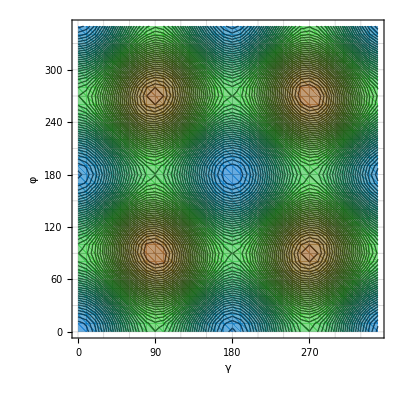

```mathematica
ListContourPlot[PotentialEnergy,
Contours->50,FrameLabel->{"γ","φ"},
FrameTicks->{Range[0,360,30],Range[0,360,30]},
GridLines->{Range[0,360,30],Range[0,360,30]},
ColorFunction->(Blend[palette,#]&)]
```

```mathematica
{γMin,γMax}=MinMax@PotentialEnergy[[;;,1]]
{φMin,φMax}=MinMax@PotentialEnergy[[;;,2]]
```

{0.,350.}

{0.,350.}

```mathematica
matr1=Cases[PotentialEnergy,{γMin,φ_,E_}]/. {γMin,φ_,E_}->{360+γMin,φ,E};
matr2=Cases[PotentialEnergy,{γMax,φ_,E_}]/. {γMax,φ_,E_}->{γMax-360,φ,E};
matr3=Cases[PotentialEnergy,{γ_,φMin,E_}]/. {γ_,φMin,E_}->{γ,360+φMin,E};
matr4=Cases[PotentialEnergy,{γ_,φMax,E_}]/. {γ_,φMax,E_}->{γ,φMax-360,E};
PotentialEnergyPlus = Join[PotentialEnergy,matr1,matr2,matr3,matr4];
```

```mathematica
Nshifts = 1;
shifts=Range[-Nshifts,Nshifts];
expandedData=Flatten[Table[Map[{#[[1]]+360*k,#[[2]]+360*l,#[[3]]}&,PotentialEnergy],{k,shifts},{l,shifts}],2];
```

```mathematica
plot2D=ListContourPlot[expandedData,
PlotRange->{{-180,540},{-180,540}},
Contours->40,
FrameLabel->{"γ","φ"},
FrameTicks->{Range[-180,540,60],Range[-180,540,60]},
GridLines->{Range[-180,540,60],Range[-180,540,60]},
ColorFunction->(Blend[palette,#]&),
ImageSize->Large];

plot3D=Plot3D[Re@Π[x,y],{x,-180,540},{y,-180,540},
ColorFunction->(Blend[palette,#3]&),
PlotPoints->50,
AxesLabel->{"x","y","f"},
ImageSize->600];
```

```mathematica
GraphicsColumn[{plot2D,plot3D}]
```

-Graphics-

### Рисуем пути

#### Находим минимумы

Критические точки

```mathematica
vars={x,y};
δ=1;
func=ComplexExpand[Re[Π[x,y]],vars];
eqs=Thread[Grad[func,vars]==0];
limits=Thread[0-δ<vars<360+δ];

Criticalpoints=vars/. NSolve[Join[eqs,limits],vars,WorkingPrecision->30]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{-0.147876,269.437},{0,0},{0,180.},{0,360.},{0.147876,90.5633},{89.4367,179.852},{90.,90.},{90.,270.},{90.5633,0.147876},{90.5633,360.148},{179.852,89.4367},{180.,0},{180.,180.},{180.,360.},{180.148,270.563},{269.437,-0.147876},{269.437,359.852},{270.,90.},{270.,270.},{270.563,180.148},{359.852,269.437},{360.,0},{360.,180.},{360.,360.},{360.148,90.5633}}

```mathematica
plot3d=Plot3D[func,{x,0,360},{y,0,360},ColorFunction->"TemperatureMap",PlotPoints->50,AxesLabel->{"x","y","f"}];

points3d=Graphics3D[{Red,PointSize[0.02],Point[{#[[1]],#[[2]],Re[Π[#[[1]],#[[2]]]]}&/@Criticalpoints]}];

Show[plot3d,points3d]
```

-Graphics3D-

Стационарные точки и Минимумы

```mathematica
hessian[f_,vars_List]:=D[f,{vars,2}]
```

```mathematica
hessian[Π[x,y],{x,y}]/. Thread[{x,y}->#]&/@Criticalpoints//Chop;
eigenvals=Eigenvalues[#]&/@%;
statiomaryindices=Flatten[Position[Times@@@eigenvals,_?Negative,{1}]];
minimumindices=Flatten[Position[eigenvals,_?(AllTrue[#,Positive]&),{1}]]//Rest;
StationaryPoints=Criticalpoints[[statiomaryindices]];
MinPoints=Criticalpoints[[minimumindices]];
```

```mathematica
plot3d=Plot3D[func,{x,0,360},{y,0,360},ColorFunction->(Blend[palette,#3]&),PlotPoints->50,AxesLabel->{"ϕ","γ","Π"},LabelStyle->Directive[FontSize->18,Bold,FontFamily->"Times"],ImageSize->Large];

points3d=Graphics3D[{Red,PointSize[0.02],Point[{#[[1]],#[[2]],Re[Π[#[[1]],#[[2]]]]}&/@StationaryPoints],Black,PointSize[0.02],Point[{#[[1]],#[[2]],Re[Π[#[[1]],#[[2]]]]}&/@MinPoints]}];

Legended[Show[plot3d,points3d,AxesLabel->{"ϕ","γ","Π"},LabelStyle->Directive[FontSize->16,Bold]],PointLegend[{Red,Black},{"Седловые точки","Минимумы"},LegendMarkerSize->20,LabelStyle->Directive[FontSize->30,Black,FontFamily->"Times"]]]
```

-Graphics3D-

#### Начальные данные

```mathematica
{idx1,idx2}=RandomSample[Range[Length[MinPoints]],2]
min1=MinPoints[[idx1]];(*idx1*)
min2=MinPoints[[idx2]];(*idx2*)
stepSize=0.2;
iterations=500;
threshold=0.5;
numPaths=2;
```

{5,7}

#### Остальное

Ближайшие минимумы, зачем-то

```mathematica
RestMins=Delete[MinPoints,{{idx1},{idx2}}];
ClosestMins=Nearest[RestMins,min1,2];
```

Находим стационарные точки через которые проходят пути

```mathematica
midpoint=(min1+min2)/2
closestIndexes=Flatten@Nearest[StationaryPoints->Automatic,midpoint,1]
```

{270.,90.}

{6}

```mathematica
selectedPoint=StationaryPoints[[closestIndexes]]
```

{{179.852,89.4367}}

```mathematica
dist12=EuclideanDistance[min1,min2];
tolerance=1.2;

selectedPoint=Select[StationaryPoints,(EuclideanDistance[#,min1]+EuclideanDistance[#,min2])<(dist12*tolerance)&];
```

```mathematica
selectedPoints3D=Append[#,Re[Π@@#]]&/@selectedPoint;
allMinForPaths3D=Append[#,Re[Π@@#]]&/@Prepend[ClosestMins,min1];
MinMaxForGraph3D=Append[#,Re[Π@@#]]&/@{min1,min2};
```

Строим пути

```mathematica
(*colors=Reverse[ColorData[20,"ColorList"]][[;;Length[prtracks]]];*)
colors={Black,Red,Blue,Purple,Yellow,Green,Orange};
```

```mathematica
tracks=Re[BuildTrackFromPoint[Π,#,stepSize,iterations,threshold,MinPoints]&/@selectedPoint]//Chop;
prtracks=tracks[[All,All,;;2]];
```

```mathematica
paths2D=Table[ListPlot[prtracks[[n]],PlotStyle->colors[[n]],Joined->True,PlotLegends->None],{n,1,Length@tracks}];
```

```mathematica
paths3D=Graphics3D[Join[Table[{colors[[n]],Thickness[0.005],Line[tracks[[n]]]},{n,1,Length@tracks}],{Green,PointSize[0.03],Point[Append[min1,Re@Π@@min1]],Red,PointSize[0.03],Point[Append[min2,Re@Π@@min2]],Blue,PointSize[0.025],Point[Append[StationaryPoints[[closestIndexes]],Re@Π@@StationaryPoints[[closestIndexes]]]],Gray,PointSize[0.01],Point[Append[#,Re@Π@@#]&/@StationaryPoints]}]];
```

Палитра для 2D путей, нумерация для стационарных точек и минимумов

```mathematica
redLabels=Table[Text[Style[i,Red,20,Bold],selectedPoint[[i, ;;2]],{-1.5,-1.5}],{i,Length[selectedPoint]}];
redPoints=Graphics[{Red,PointSize[0.02],Point[selectedPoint[[All, ;;2]]]}];

allMinForPaths=Prepend[ClosestMins,min1];
blueLabels=Table[Text[Style[i,Cyan,20,Bold],allMinForPaths[[i, ;;2]],{1.5,1.5}],{i,Length[allMinForPaths]}];
bluePoints=Graphics[{Cyan,PointSize[0.02],Point[allMinForPaths[[All, ;;2]]]}];

blackLabels=Table[Text[Style[i,Black,20,Bold],{min1,min2}[[i, ;;2]],{1.5,1.5}],{i,1,2}];
blackPoints=Graphics[{Black,PointSize[0.02],Point[{min1,min2}[[All, ;;2]]]}];

allLabels=Join[redLabels,blueLabels,blackLabels];
xGrid=Range[-360,540,360];
yGrid=Range[-360,540,360];
```

```mathematica
plot2D=ListContourPlot[expandedData,PlotRange->{{-10,370},{-10,370}},Contours->40,FrameLabel->{"γ","φ"},FrameStyle->Directive[Black,Thickness[0.002]],LabelStyle->Directive[FontSize->18,Bold],FrameTicks->{Range[-180,540,60],Range[-180,540,60]},GridLines->{Range[-180,540,60],Range[-180,540,60]},ColorFunction->(Blend[palette,#]&),ImageSize->Large]
```

-Graphics-

```mathematica
finalPlot2D=Show[plot2D,paths2D,redPoints,bluePoints,blackPoints,Graphics[allLabels],GridLines->{xGrid,yGrid},GridLinesStyle->Directive[LightGray,Dashed,AbsoluteThickness[1]]];
```

Палитра для 3D путей, нумерация для стационарных точек и минимумов

```mathematica
{zMin,zMax}=MinMax[Flatten[{selectedPoints3D[[All,3]],allMinForPaths3D[[All,3]]}]];
dz=0.5 (zMax-zMin);

paths3DLines=Graphics3D[Table[{colors[[n]],Thickness[0.005],Line[tracks[[n]]]},{n,1,Length[tracks]}]];

redPoints3D=Graphics3D[{Red,PointSize[0.02],Point[selectedPoints3D]}];
redLabels3D=Table[Graphics3D[Text[Style[i,Red,20,Bold],selectedPoints3D[[i]]+{0,0,dz}]],{i,Length[selectedPoints3D]}];

bluePoints3D=Graphics3D[{Cyan,PointSize[0.02],Point[allMinForPaths3D]}];
blueLabels3D=Table[Graphics3D[Text[Style[i,Cyan,20,Bold],allMinForPaths3D[[i]]+{0,0,dz}]],{i,1,Length[allMinForPaths3D]}];

blackPoints3D=Graphics3D[{Black,PointSize[0.02],Point[MinMaxForGraph3D]}];
blackLabels3D=Table[Graphics3D[Text[Style[i,Black,20,Bold],MinMaxForGraph3D[[i]]+{0,0,dz}]],{i,Length[MinMaxForGraph3D]}];
```

```mathematica
plot3d=Plot3D[func,{x,-10,370},{y,-10,370},ColorFunction->(Blend[palette,#3]&),PlotPoints->50,AxesLabel->{"γ","ϕ","Π"},LabelStyle->Directive[FontSize->18,Bold],ImageSize->Large];
```

```mathematica
finalPlot3D=Show[plot3d,paths3DLines,redPoints3D,bluePoints3D,blackPoints3D,redLabels3D,blueLabels3D,blackLabels3D,Axes->True,Boxed->True,ImageSize->600];
```

Финальный 2D+3D график

```mathematica
finalPlot=Grid[{{"2D","3D"},{finalPlot2D,finalPlot3D}}]
```

2D | 3D
-Graphics- | -Graphics3D-

```mathematica
findChain[allTracks_,start_,end_,threshold_:0.01]:=Module[{currentPos=start[[1;;2]],targetPos=end[[1;;2]],path={},remaining=allTracks,found,nextSeg,distToStart,distToEnd},While[EuclideanDistance[currentPos,targetPos]>threshold&&Length[remaining]>0,found=False;
Do[nextSeg=remaining[[i]];
distToStart=EuclideanDistance[currentPos,nextSeg[[1,1;;2]]];
distToEnd=EuclideanDistance[currentPos,nextSeg[[-1,1;;2]]];
If[distToStart<threshold||distToEnd<threshold,If[distToEnd<distToStart,nextSeg=Reverse[nextSeg]];
AppendTo[path,nextSeg];
currentPos=nextSeg[[-1,1;;2]];
remaining=Delete[remaining,i];
found=True;
Break[];],{i,Length[remaining]}];
If[!found,Break[]];];
Flatten[path,1]//DeleteDuplicates]

fullPath=findChain[tracks,min1,min2];
```

```mathematica
coords=fullPath[[All,1;;2]];
energies=fullPath[[All,3]];
stepDistances=MapThread[EuclideanDistance,{Drop[coords,-1],Rest[coords]}];
cumulativeDist=Prepend[Accumulate[stepDistances],0];
```

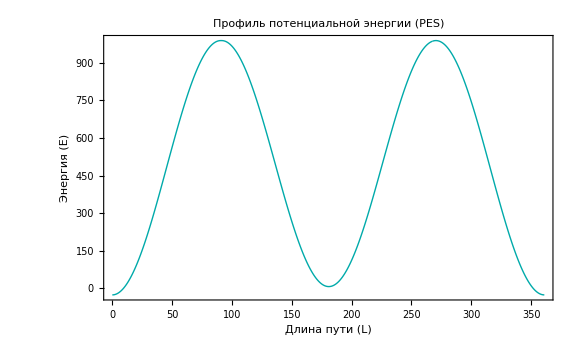

```mathematica
ListLinePlot[Transpose[{cumulativeDist,energies}],PlotStyle->{Thick,Darker@Cyan},Frame->True,FrameLabel->{"Длина пути (L)","Энергия (E)"},PlotLabel->"Профиль потенциальной энергии (PES)",InterpolationOrder->2,FillingStyle->LightBlue,ImageSize->Large]
```

```mathematica
lineDist=EuclideanDistance[min1,min2];
plotAnalytical=Plot[Re[Π@@(min1+s/lineDist*(min2-min1))],{s,0,lineDist},PlotStyle->{Red,Dashed},PlotLabels->Placed["Прямая линия (аналитика)",Above]];


If[Length[fullPath]>0,coords=fullPath[[All,1;;2]];
energies=fullPath[[All,3]];
stepDistances=MapThread[EuclideanDistance,{Drop[coords,-1],Rest[coords]}];
cumulativeDist=Prepend[Accumulate[stepDistances],0];
lineDist=EuclideanDistance[min1[[1;;2]],min2[[1;;2]]];
integralTracks=Total[MovingAverage[energies,2]*stepDistances];
fAnalytic[s_]:=Re[Π@@(min1[[1;;2]]+s/lineDist*(min2[[1;;2]]-min1[[1;;2]]))];
integralAnalytic=NIntegrate[fAnalytic[s],{s,0,lineDist}];
Print["Результаты интегрирования:"];
Print["По криволинейному пути: ",integralTracks];
Print["По прямой линии: ",integralAnalytic];
yMin=-100;
yMax=Max[energies,Max[Table[fAnalytic[s],{s,0,lineDist,lineDist/20}]]];
yTicks=Range[yMin,yMax+200,200];
plotAnalytical=Plot[fAnalytic[s],{s,0,lineDist},PlotStyle->{Red,Dashed,Thick}];
plotTracks=ListLinePlot[Transpose[{cumulativeDist,energies}],PlotStyle->{Thick,Blue},InterpolationOrder->2];
Show[plotTracks,plotAnalytical,Frame->True,FrameTicks->{{yTicks,yTicks},{Automatic,Automatic}},PlotRange->{All,{yMin,Automatic}},FrameLabel->{{"Энергия","Энергия"},{"Расстояние от min1 (L)",None}},GridLines->{Automatic,yTicks},PlotLabel->Column[{Style["Сравнение профилей потенциальной энергии",Bold,14],Row[{Style["∫ (синий) = ",Blue],NumberForm[integralTracks,{10,4}]}],Row[{Style["∫ (красный) = ",Red],NumberForm[integralAnalytic,{10,4}]}]},Center],ImageSize->Large,BaseStyle->{FontSize->12}],Print["Цепочка не найдена!"]]
```

Результаты интегрирования:

По криволинейному пути: 176933.

По прямой линии: 255018.

```mathematica
If[Length[fullPath]>0,coords=fullPath[[All,1;;2]];
energies=fullPath[[All,3]];
stepDistances=MapThread[EuclideanDistance,{Drop[coords,-1],Rest[coords]}];
cumulativeDist=Prepend[Accumulate[stepDistances],0];
lineDist=EuclideanDistance[min1,min2];
integralTracks=Total[MovingAverage[energies,2]*stepDistances];
fAnalytic[s_]:=Re[Π@@(min1+s/lineDist*(min2-min1))];
integralAnalytic=NIntegrate[fAnalytic[s],{s,0,lineDist}];
palette={RGBColor[0.0,0.45,0.8,0.6],RGBColor[0.2,0.8,0.2,0.6],RGBColor[0.6,0.35,0.1,0.6]};
yMin=-100;
yMax=Max[energies,Max[Table[fAnalytic[s],{s,0,lineDist,lineDist/20}]]];
yTicks=Range[yMin,yMax+200,200];
xMax=Max[cumulativeDist,lineDist];
xGridLines=Range[0,xMax,50];
xTickValues=Range[0,xMax,50];
bottomTicks=Transpose[{xTickValues,ToString[#]<>"°"&/@xTickValues}];
plotAnalytical=Plot[fAnalytic[s],{s,0,lineDist},PlotStyle->{Blue,Thickness[0.01]}];
plotTracks=ListLinePlot[Transpose[{cumulativeDist,energies}],PlotStyle->{Red,Thickness[0.01]},InterpolationOrder->2];
plotTracksGreenDashed=ListLinePlot[Transpose[{cumulativeDist,energies}],PlotStyle->{Green,Thickness[0.005],Dashing[{0.02}]},InterpolationOrder->2];
eigenvalueLines={GrayLevel[0.1],Thickness[0.001],Dashing[{0.01,0.002}],Line[{{0,#},{xMax,#}}]&/@eigenvalues};
Show[plotAnalytical,plotTracks,plotTracksGreenDashed,Prolog->{Texture[None],LinearGradientFilling[palette,Top],Rectangle[Offset[{0,0},Scaled[{0,0}]],Offset[{0,0},Scaled[{1,1}]]]},Epilog->{AbsoluteThickness[6],Black,Line[{{0,0},{xMax,0}}],eigenvalueLines},Frame->True,FrameTicks->{{yTicks,yTicks},{bottomTicks,None}},PlotRange->{{0,xMax},{yMin,yMax+50}},PlotRangeClipping->True,FrameLabel->{{Style["Энергия",18,Bold],Style["Энергия",18,Bold]},{None,None}},GridLines->{xGridLines,yTicks},ImageSize->Large,BaseStyle->{FontSize->18}]]
```

-Graphics-

## Решение для молекул с 3 углами

### Импорт данных

```mathematica
SetDirectory@NotebookDirectory[]
Import["B(OH)3 PE.xlsx","Sheets"]
Dimensions[DataAll=Import["B(OH)3 PE.xlsx",{"Data",1}]]
Length[PotentialEnergy=DataAll[[2;;,4]]]
```

D:\Andrei\2 Курс\Курсовая

{B(OH)3}

{46657,4}

46656

```mathematica
Min[PotentialEnergy]
```

0.

### Функция отображения 3-х мерного графика

```mathematica
f[x_,y_,z_]:=0.003 x+0.002 y+0.0025 z+15 ⅇ^(-((x-80)^2/2000+(y-120)^2/1800+(z-90)^2/2200))+12 ⅇ^(-((x-200)^2/3000+(y-180)^2/2500+(z-150)^2/2800))10 ⅇ^(-((x-300)^2/3500+(y-250)^2/3000+(z-200)^2/3200))+8 ⅇ^(-((x-150)^2/4000+(y-80)^2/3500+(z-280)^2/3800))-9 ⅇ^(-((x-50)^2/2500+(y-250)^2/2200+(z-100)^2/2600))-7 ⅇ^(-((x-280)^2/3200+(y-60)^2/2800+(z-50)^2/3000))-6 ⅇ^(-((x-120)^2/3800+(y-300)^2/3500+(z-180)^2/4000))+-5*ⅇ^(-((x-250)^2/4200+(y-200)^2/3800+(z-300)^2/4500))+3 Sin[0.015 x] Cos[0.02 y] Sin[0.012 z]+2.5 Sin[0.012 x+1] Cos[0.018 y+0.5] Sin[0.01 z+1.2]+2 Sin[0.025 x] Sin[0.016 y] Cos[0.02 z]+1.8 Sin[0.01 x+0.3] Cos[0.025 y] Sin[0.015 z+1.5]+1.5 Cos[0.02 x] Sin[0.014 y+0.7] Cos[0.018 z]+0.8 Sin[0.5 10^-4 x y] Cos[0.4 10^-4 y z] Sin[0.3 10^-4 x z]+0.6 Sin[0.035 x+2.1] Sin[0.022 y+1.3] Cos[0.028 z+0.9]+0.4 Cos[0.03 x+0.2] Cos[0.019 y+0.8] Cos[0.024 z+1.1]+0.3 ⅇ^(-10^-3*(x^2+y^2+z^2)) Sin[0.04 x] Cos[0.03 y] Sin[0.035 z];
```

```mathematica
f[x_,y_,z_]:=Sin[x Degree]+Cos[y Degree]+Sin[z Degree];
```

```mathematica
n=16;
step=360/n;
gap=step 0.02;
realStep=step-gap;
opacity=0.1;

data=Flatten[Table[f[x,y,z],{x,0,360,step},{y,0,360,step},{z,0,360,step}]];
minVal=Min[data];
maxVal=Max[data];
midVal=Mean[data];

dist=Max[maxVal-midVal,midVal-minVal];

cubes=Flatten[Table[cx=(i-0.5) step;cy=(j-0.5) step;cz=(k-0.5) step;
val=f[cx,cy,cz];
color=Blend[{Blue,White,Red},Rescale[val,{midVal-dist,midVal+dist}]];
{EdgeForm[None],Append[color,opacity],Cuboid[{(i-1) step+gap/2,(j-1) step+gap/2,(k-1) step+gap/2},{(i-1) step+gap/2+realStep,(j-1) step+gap/2+realStep,(k-1) step+gap/2+realStep}]},{i,1,n},{j,1,n},{k,1,n}],2];

Graphics3D[{cubes},Boxed->True,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->500,ViewPoint->{3,1,1},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
gridSize=30;
stepSize=360/(gridSize-1);

data=ParallelTable[f[x,y,z],{x,0,360,stepSize},{y,0,360,stepSize},{z,0,360,stepSize}];

fInterp=ListInterpolation[data,{{0,360},{0,360},{0,360}},InterpolationOrder->1];

actualMin=Min[data];
actualMax=Max[data];
midVal=Mean[Flatten[data]];

dist=Max[actualMax-midVal,midVal-actualMin];
colorMin=midVal-dist;
colorMax=midVal+dist;

Manipulate[SliceContourPlot3D[fInterp[x,y,z],z==pos,{x,0,360},{y,0,360},{z,0,360},Contours->15,PlotPoints->25,MaxRecursion->0,PerformanceGoal->"Speed",ColorFunction->(Blend[{Blue,White,Red},Rescale[#1,{colorMin,colorMax}]]&),ColorFunctionScaling->False,BoxRatios->{1,1,1},ImageSize->Medium,AxesLabel->{"X","Y","Z"}],{{pos,180,"Положение Z"},0,360}]
```

colorMin
Blend::argl: -(-------------------)
               colorMax - colorMin
     should be a real number or a list of non-negative numbers, which has the
     same length as {RGBColor[0, 0, 1], GrayLevel[1], RGBColor[1, 0, 0]}.

360                   colorMin
Blend::argl: ------------------------ - -------------------
             17 (colorMax - colorMin)   colorMax - colorMin
     should be a real number or a list of non-negative numbers, which has the
     same length as {RGBColor[0, 0, 1], GrayLevel[1], RGBColor[1, 0, 0]}.

720                   colorMin
Blend::argl: ------------------------ - -------------------
             17 (colorMax - colorMin)   colorMax - colorMin
     should be a real number or a list of non-negative numbers, which has the
     same length as {RGBColor[0, 0, 1], GrayLevel[1], RGBColor[1, 0, 0]}.

General::stop: Further output of Blend::argl
     will be suppressed during this calculation.

colorMin
Blend::argl: -(-------------------)
               colorMax - colorMin
     should be a real number or a list of non-negative numbers, which has the
     same length as {RGBColor[0, 0, 1], GrayLevel[1], RGBColor[1, 0, 0]}.

360                   colorMin
Blend::argl: ------------------------ - -------------------
             17 (colorMax - colorMin)   colorMax - colorMin
     should be a real number or a list of non-negative numbers, which has the
     same length as {RGBColor[0, 0, 1], GrayLevel[1], RGBColor[1, 0, 0]}.

720                   colorMin
Blend::argl: ------------------------ - -------------------
             17 (colorMax - colorMin)   colorMax - colorMin
     should be a real number or a list of non-negative numbers, which has the
     same length as {RGBColor[0, 0, 1], GrayLevel[1], RGBColor[1, 0, 0]}.

General::stop: Further output of Blend::argl
     will be suppressed during this calculation.

### Матрицы значений

#### Базисы

```mathematica
ClearAll[funs1,funs1,K]
K=3;
```

```mathematica
funs1[γ_,φ_,θ_]=Function[{γ,φ,θ},Evaluate[DeleteCases[Union[Flatten@Table[{f[(m γ+n φ+p θ)°]},{m,0,K},{n,0,K},{p,0,K},{f,{Cos,Sin}}]/. {Cos[x_]:>(ⅇ^(ⅈ x)+ⅇ^(-ⅈ x))/2,Sin[x_]:>(ⅇ^(ⅈ x)-ⅇ^(-ⅈ x))/(2ⅈ)}],0]]];
funs2[γ_,φ_,θ_]=Function[{γ,φ,θ},Evaluate[Flatten@Table[E^(I (m γ+n φ+k θ) Degree),{m,-K,K},{n,-K,K},{k,-K,K}]]];
```

#### Матрица перехода

```mathematica
H=1;
grid=Flatten[Table[{g,p,q},{g,-360. H,360 H,50},{p,-360. H,360 H,50},{q,-360. H,360 H,50}],2];

M1=funs1[γ,φ,θ]@@@grid;
M2=funs2[γ,φ,θ]@@@grid;
Dimensions[S=Transpose[LeastSquares[M2,M1]]]
```

{127,343}

```mathematica
ClearAll[g,p,q]
Dimensions[M=Flatten[Table[funs1[g,p,q][γ,φ,θ],{γ,0.,350,10},{φ,0.,350,10},{θ,0.,350,10}],2]//Chop]
```

{46656,127}

### Аппроксимация

#### Вычисления

```mathematica
ClearAll[Inf]
Inf[{γ_Integer/;Mod[γ,10]==0,ϕ_Integer/;Mod[ϕ,10]==0,θ_Integer/;Mod[θ,10]==0}]:=DataAll[[2;;,4]][[1+1296 γ/10+36 ϕ/10+θ/10]];
```

```mathematica
ClearAll[Π]
Map[Dimensions,{U,Σ,V}=SingularValueDecomposition[M,Length@funs1[g,p,q][γ,φ,θ]]]
Diagonal@Σ
coef=V.((Uᵀ.DataAll[[2;;,4]])/(Diagonal@Σ))//Chop
Π[γ_,φ_,θ_]:=coef.funs1[g,p,q][γ,φ,θ]
```

{{46656,127},{127,127},{127,127}}

{216.,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735,152.735}

{5309.22,0,2.34877×10^-10,0,-1623.59,1.35259×10^-10,1.69834×10^-10,0,0,0,-1623.59,0,0,0,-300.501,0,41.199,0,-10.7598,0,-41.199,0,220.613,0,-3.34581,0,-10.7598,0,3.34581,0,0.394284,0,0,0,-1623.59,0,0,0,-300.501,0,-41.199,0,-10.7598,0,-300.501,0,0,0,4.8351,0,0,0,41.199,0,4.8351,0,0,0,-0.852749,0,-10.7598,0,0,0,-0.852749,0,0,0,41.199,0,220.613,0,3.34581,0,-41.199,0,4.8351,0,0,0,-0.852749,0,220.613,0,0,0,-14.0419,0,0,0,-3.34581,0,-0.852749,0,0,0,0.0878658,0,-10.7598,0,-3.34581,0,0.394284,0,-10.7598,0,0,0,-0.852749,0,0,0,3.34581,0,-0.852749,0,0,0,0.0878658,0,0.394284,0,0,0,0.0878658,0,0}

#### Графики

```mathematica
n=16;
step=360/n;
gap=step 0.02;
realStep=step-gap;
opacity=0.1;

data=Flatten[Table[Re[Π[x,y,z]],{x,0,360,step},{y,0,360,step},{z,0,360,step}]];
minVal=Min[data];
maxVal=Max[data];
midVal=Mean[data];

dist=Max[maxVal-midVal,midVal-minVal];

cubes=Flatten[Table[cx=(i-0.5) step;cy=(j-0.5) step;cz=(k-0.5) step;
val=Re[Π[cx,cy,cz]];
color=Blend[{Blue,White,Red},Rescale[val,{midVal-dist,midVal+dist}]];
{EdgeForm[None],Append[color,opacity],Cuboid[{(i-1) step+gap/2,(j-1) step+gap/2,(k-1) step+gap/2},{(i-1) step+gap/2+realStep,(j-1) step+gap/2+realStep,(k-1) step+gap/2+realStep}]},{i,1,n},{j,1,n},{k,1,n}],2];

plot3D=Graphics3D[{cubes},Boxed->True,BoxRatios->{1,1,1},Axes->True,AxesLabel->{"X","Y","Z"},ImageSize->500,ViewPoint->{3,1,1},Lighting->"Neutral"]
```

-Graphics3D-

```mathematica
gridSize=30;
stepSize=360/(gridSize-1);

data=ParallelTable[Re[Π[x,y,z]],{x,0,360,stepSize},{y,0,360,stepSize},{z,0,360,stepSize}];

fInterp=ListInterpolation[data,{{0,360},{0,360},{0,360}},InterpolationOrder->1];

actualMin=Min[data];
actualMax=Max[data];
midVal=Mean[Flatten[data]];

dist=Max[actualMax-midVal,midVal-actualMin];
colorMin=midVal-dist;
colorMax=midVal+dist;

Manipulate[SliceContourPlot3D[fInterp[x,y,z],z==pos,{x,0,360},{y,0,360},{z,0,360},Contours->15,PlotPoints->25,MaxRecursion->0,PerformanceGoal->"Speed",ColorFunction->(Blend[{Blue,White,Red},Rescale[#1,{colorMin,colorMax}]]&),ColorFunctionScaling->False,BoxRatios->{1,1,1},ImageSize->Medium,AxesLabel->{"X","Y","Z"}],{{pos,180,"Положение Z"},0,360}]
```

```mathematica
1/36^3 Plus@@Abs[Flatten[Table[Re[Π[γ,φ,θ]]-Inf[{γ,φ,θ}],{γ,0,350,10},{φ,0,350,10},{θ,0,350,10}]]]
```

$Aborted

```mathematica
MinMax@Abs[Flatten[Table[Re[Π[γ,φ,θ]]-Inf[{γ,φ,θ}],{γ,0,350,10},{φ,0,350,10},{θ,0,350,10}]]]
```

{0.0464494,382.276}

#### Генерация GIF анимации

```mathematica
gridSize=30;
stepSize=360/(gridSize-1);

data=ParallelTable[Re[Π[x,y,z]],{x,0,360,stepSize},{y,0,360,stepSize},{z,0,360,stepSize}];

fInterp=ListInterpolation[data,{{0,360},{0,360},{0,360}},InterpolationOrder->1];

actualMin=Min[data];
actualMax=Max[data];
midVal=Mean[Flatten[data]];
dist=Max[actualMax-midVal,midVal-actualMin];
colorMin=midVal-dist;
colorMax=midVal+dist;

frames=Table[SliceContourPlot3D[fInterp[x,y,z],z==pos,{x,0,360},{y,0,360},{z,0,360},Contours->15,PlotPoints->25,MaxRecursion->0,PerformanceGoal->"Speed",ColorFunction->(Blend[{Blue,White,Red},Rescale[#1,{colorMin,colorMax}]]&),ColorFunctionScaling->False,BoxRatios->{1,1,1},ImageSize->Medium,AxesLabel->{"γ","φ","θ"},Background->White,AxesStyle->Black,BoxStyle->Black,LabelStyle->Directive[Black,12]],{pos,0,360,10}];

Export["slice_animation.gif",frames,"AnimationRepetitions"->Infinity,"DisplayDurations"->0.1]
```

slice_animation.gif

### Рисуем пути

#### Находим минимумы

Критические точки

```mathematica
vars={x,y,z};
δ=10;
func=ComplexExpand[Re[Π[x,y,z]],vars];
eqs=Thread[Grad[func,vars]==0];
limits=Thread[0-δ<vars<360+δ];
```

```mathematica
funcClean=ComplexExpand[Re[Π[x,y,z]]];
gradSym=Grad[funcClean,vars];
gradFunc[xv_?NumericQ,yv_?NumericQ,zv_?NumericQ]:=gradSym/. {x->xv,y->yv,z->zv};

grid=Flatten[Table[{xv,yv,zv},{xv,0,360,60},{yv,0,360,60},{zv,0,360,60}],2];

rawPoints=Quiet[ParallelMap[Check[vars/. FindRoot[gradFunc[x,y,z],Thread[{vars,#}]],Nothing]&,grid]];

Criticalpoints=DeleteDuplicates[rawPoints,(Norm[#1-#2]<10^-4&)];

Criticalpoints=Select[Criticalpoints,AllTrue[#,(0-δ<=#<=360+δ&)]&]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal, but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{{-4.22674×10^-12,-3.90013×10^-13,-3.90013×10^-13},{-2.8772,-4.2386,95.3635},{-4.89723×10^-12,-9.96306×10^-13,180.},{2.8772,4.2386,264.636},{-4.22674×10^-12,-3.90013×10^-13,360.},{-4.2386,95.3635,-2.8772},{-4.84312,91.423,91.7797},{-3.11351,90.,183.114},{-6.096×10^-12,180.,360.},{-1.35242,93.8682,268.23},{-4.2386,95.3635,357.123},{-4.22688×10^-12,360.,-3.91812×10^-13},{-6.08504×10^-12,180.,-9.96306×10^-13},{-2.01653,182.017,90.},{-7.10286×10^-12,180.,180.},{2.01653,177.983,270.},{4.2386,264.636,2.8772},{1.35242,266.132,91.7697},{3.11351,270.,176.886},{4.84312,268.577,268.22},{4.2386,264.636,362.877},{-4.90157×10^-12,360.,180.},{-2.8772,355.761,95.3635},{2.8772,364.239,264.636},{-4.22674×10^-12,360.,360.},{95.3635,-2.8772,-4.2386},{180.,1.56144×10^-12,2.38371×10^-12},{91.7797,-4.84312,91.423},{90.,-2.01653,182.017},{360.,-3.90912×10^-13,-3.89672×10^-13},{91.7697,1.35242,266.132},{95.3635,-2.8772,355.761},{180.,180.,180.},{90.,90.,90.},{88.2203,88.577,184.843},{88.7853,91.2147,270.},{91.423,91.7797,-4.84312},{91.423,91.7797,355.157},{90.,183.114,-3.11351},{88.577,184.843,88.2203},{84.6365,184.239,182.877},{86.1318,181.352,271.77},{90.,183.114,356.886},{180.,360.,2.38729×10^-12},{183.114,356.886,90.},{180.,360.,180.},{176.886,363.114,270.},{180.,360.,360.},{93.8682,268.23,-1.35242},{91.2147,270.,88.7853},{88.2303,273.868,178.648},{90.,271.215,268.785},{93.8682,268.23,358.648},{95.3635,357.123,-4.2386},{90.,357.983,182.017},{360.,360.,-3.9172×10^-13},{91.7697,361.352,266.132},{95.3635,357.123,355.761},{180.,180.,2.38862×10^-12},{360.,-3.90223×10^-13,360.},{91.7797,355.157,91.423},{183.114,-3.11351,90.},{180.,1.56597×10^-12,180.},{176.886,3.11351,270.},{180.,1.56597×10^-12,360.},{182.017,90.,-2.01653},{184.843,88.2203,88.577},{182.877,84.6365,184.239},{180.,180.,360.},{178.648,88.2303,273.868},{182.017,90.,357.983},{184.239,182.877,84.6365},{175.761,177.123,275.364},{181.352,271.77,86.1318},{177.123,275.364,175.761},{175.157,271.78,271.423},{177.983,270.,362.017},{177.983,270.,2.01653},{264.636,2.8772,4.2386},{360.,-9.98182×10^-13,180.},{268.23,-1.35242,93.8682},{270.,2.01653,177.983},{268.22,4.84312,268.577},{264.636,2.8772,364.239},{270.,88.7853,91.2147},{268.785,90.,271.215},{266.132,91.7697,1.35242},{356.886,90.,183.114},{271.77,86.1318,181.352},{266.132,91.7697,361.352},{270.,176.886,3.11351},{360.,180.,180.},{273.868,178.648,88.2303},{275.364,175.761,177.123},{271.423,175.157,271.78},{270.,176.886,363.114},{268.577,268.22,4.84312},{271.215,268.785,90.},{360.,360.,360.},{270.,270.,270.},{268.577,268.22,364.843},{363.114,270.,176.886},{271.78,271.423,175.157},{264.636,362.877,4.2386},{360.,360.,180.},{268.23,358.648,93.8682},{270.,362.017,177.983},{268.22,364.843,268.577},{264.636,362.877,364.239},{360.,180.,-9.93073×10^-13},{360.,180.,360.},{357.123,-4.2386,95.3635},{362.877,4.2386,264.636},{355.761,95.3635,-2.8772},{355.157,91.423,91.7797},{358.648,93.8682,268.23},{355.761,95.3635,357.123},{357.983,182.017,90.},{362.017,177.983,270.},{364.239,264.636,2.8772},{361.352,266.132,91.7697},{364.843,268.577,268.22},{364.239,264.636,362.877},{357.123,355.761,95.3635},{362.877,364.239,264.636}}

```mathematica
EuclideanDistance[Criticalpoints[[#]],Criticalpoints[[#+1]]]&/@Range[Length@Criticalpoints-1]
```

{95.501,84.7914,84.7914,95.501,375.223,94.7408,91.3612,198.491,125.866,88.9519,444.508,180.,90.0452,90.0452,90.0452,280.835,88.9519,85.2228,91.3612,94.7408,206.292,84.7914,169.583,95.501,522.919,84.7914,127.139,90.6551,325.629,377.856,89.8012,267.394,155.885,94.8705,85.1996,274.856,360.,369.732,91.3612,94.7408,88.9519,85.2228,408.359,90.1076,90.1076,90.1076,90.1076,382.643,90.1942,89.995,90.1942,89.995,373.618,186.334,325.629,377.856,89.8012,406.327,440.908,519.819,369.732,90.1076,90.1076,90.1076,373.042,90.6551,95.7489,199.986,125.866,84.2014,288.703,191.002,211.655,89.8012,95.7489,90.6551,360.,280.835,199.986,125.866,84.2014,90.6551,95.7489,286.271,180.008,269.881,203.167,85.2228,180.177,368.232,198.491,125.866,88.9519,94.7408,91.3612,369.732,85.1996,298.501,155.885,94.8705,210.4,91.3612,193.979,199.986,125.866,84.2014,90.6551,95.7489,418.579,360.,322.466,169.583,282.698,94.7408,176.502,88.9519,280.835,180.09,280.835,88.9519,176.502,94.7408,282.698,169.583}

```mathematica
points3d=Graphics3D[{Red,Sphere[Criticalpoints,5] }];

Manipulate[Show[SliceContourPlot3D[fInterp[x,y,z],z==pos,{x,0,360},{y,0,360},{z,0,360},
PlotRange->{{0,360},{0,360},{0,360}},
ColorFunctionScaling->False,
ColorFunction->(Blend[{Blue,White,Red},Rescale[#1,{colorMin,colorMax}]]&),
Contours->20,
ContourStyle->None,
PlotPoints->40,
BoxRatios->{1,1,1},
AxesLabel->{"X","Y","Z"},
ViewPoint->{2,2,1.5}],
points3d,
PlotRange->{{0,360},{0,360},{0,360}},
BoxRatios->{1,1,1}],
{{pos,180,"Положение Z"},0,360,Appearance->"Labeled"},ControlPlacement->Top]
```

Стационарные точки и Минимумы

```mathematica
hessian[f_,vars_List]:=D[f,{vars,2}]
```

```mathematica
(*Гессиан в каждой критической точке*)
hessMat=hessian[Π[x,y,z],{x,y,z}]/. Thread[{x,y,z}->#]&/@Criticalpoints//Chop;
eigenvals=Eigenvalues[#]&/@hessMat;
morseIndices=Count[#,_?Negative]&/@eigenvals;

eps=5.0;
filteredCriticalpoints=Select[Criticalpoints,Max[#]<=360-eps&];

hessMatFiltered=hessian[Π[x,y,z],{x,y,z}]/. Thread[{x,y,z}->#]&/@filteredCriticalpoints//Chop;
eigenvalsFiltered=Eigenvalues[#]&/@hessMatFiltered;
morseIndicesFiltered=Count[#,_?Negative]&/@eigenvalsFiltered;

statiomaryindicesFiltered=Flatten[Position[morseIndicesFiltered,1]];
minimumindicesFiltered=Flatten[Position[morseIndicesFiltered,0]];

StationaryPoints=filteredCriticalpoints[[statiomaryindicesFiltered]];
MinPoints=filteredCriticalpoints[[minimumindicesFiltered]];
```

```mathematica
points3d=Graphics3D[{Red,Sphere[StationaryPoints,5],Black,Sphere[MinPoints,5]}];

Manipulate[Show[SliceContourPlot3D[fInterp[x,y,z],z==pos,{x,0,360},{y,0,360},{z,0,360},
PlotRange->{{0,360},{0,360},{0,360}},
ColorFunctionScaling->False,
ColorFunction->(Blend[{Blue,White,Red},Rescale[#1,{colorMin,colorMax}]]&),
Contours->20,
ContourStyle->None,
PlotPoints->40,
BoxRatios->{1,1,1},
AxesLabel->{"X","Y","Z"},
ViewPoint->{2,2,1.5}],
points3d,
PlotRange->{{0,360},{0,360},{0,360}},
BoxRatios->{1,1,1}],{{pos,180,"Положение Z"},0,360,Appearance->"Labeled"},ControlPlacement->Top]
```

```mathematica
hessSaddle=hessian[Π[x,y,z],{x,y,z}]/. Thread[{x,y,z}->#]&/@StationaryPoints//Chop;
valsSaddle=Eigenvalues[#]&/@hessSaddle;
vecsSaddle=Eigenvectors[#]&/@hessSaddle;

arrowScale=40*1.3; (*увеличение на 30%*)
arrows=Flatten[Table[pt=StationaryPoints[[i]];
vl=valsSaddle[[i]];
vc=vecsSaddle[[i]];
Table[direction=vc[[j]];
color=If[vl[[j]]<0,Blue,Red];
{color,Arrowheads[0.05],Arrow[Tube[{pt,pt+arrowScale*Normalize[direction]},1.5]]},{j,1,Length[vl]}],{i,1,Length[StationaryPoints]}]];

points3dWithArrows=Graphics3D[{Black,Sphere[StationaryPoints,5],Thickness[0.003],arrows}];

points3d=Graphics3D[{Black,Sphere[StationaryPoints,5]}];

Manipulate[Show[SliceContourPlot3D[fInterp[x,y,z],z==pos,{x,0,360},{y,0,360},{z,0,360},PlotRange->{{0,360},{0,360},{0,360}},ColorFunctionScaling->False,ColorFunction->(Blend[{Blue,White,Red},Rescale[#1,{colorMin,colorMax}]]&),Contours->20,ContourStyle->None,PlotPoints->40,BoxRatios->{1,1,1},AxesLabel->{"X","Y","Z"},ViewPoint->{2,2,1.5}],points3dWithArrows,PlotRange->{{0,360},{0,360},{0,360}},BoxRatios->{1,1,1}],{{pos,180,"Положение Z"},0,360,Appearance->"Labeled"},ControlPlacement->Top]
```

#### Начальные данные

```mathematica
{idx1,idx2}=RandomSample[Range[Length[MinPoints]],2]
(*{idx1,idx2}={5,13};*) (*на 1*) 
(*{idx1,idx2}={3,19};*) (*на √2*) 
(*{idx1,idx2}={1,6};*) (*на √3*) 
(*{6,7}???*)
min1=MinPoints[[7]];(*idx1*)
min2=MinPoints[[2]];(*idx2*)
stepSize=10;
iterations=500
threshold=20;
numPaths=2;
```

{5,2}

500

```mathematica
Length@MinPoints
```

8

#### Остальное

Выбор стационарных точек (трубка)

```mathematica
RestMins=Delete[MinPoints,{{idx1},{idx2}}];
v=min2-min1;
len1=EuclideanDistance[min1,min2]
len2=v.v;

distToSegment[s_]:=Module[{t=((s-min1).v)/len2},Which[t<0.,EuclideanDistance[s,min1],t>1.,EuclideanDistance[s,min2],True,Norm[Cross[v,s-min1]]/Sqrt[len2]]];
tProjection[s_]:=((s-min1).v)/len2;
```

311.769

```mathematica
meshStep=80; 
cutoff1=  2.5  meshStep; 
cutoff2=  1.8  meshStep;
```

```mathematica
RestMins
```

{{-4.22674×10^-12,-3.90013×10^-13,-3.90013×10^-13},{-6.08504×10^-12,180.,-9.96306×10^-13},{-7.10286×10^-12,180.,180.},{180.,180.,180.},{180.,180.,2.38862×10^-12},{180.,1.56597×10^-12,180.}}

```mathematica
ClosestMins=Select[RestMins,With[{t=tProjection[#],d=distToSegment[#]},0.05<=t<=0.95&&d<=cutoff1]&];
selectedPoint=Select[StationaryPoints,With[{t=tProjection[#],d=distToSegment[#]},0.05<=t<=0.95&&d<=cutoff2]&];
```

Находим стационарные точки через которые проходят пути

```mathematica
ClosestMins
```

{{-4.22674×10^-12,-3.90013×10^-13,-3.90013×10^-13},{-6.08504×10^-12,180.,-9.96306×10^-13},{-7.10286×10^-12,180.,180.},{180.,180.,180.},{180.,1.56597×10^-12,180.}}

```mathematica
selectedPoints4D=Append[#,Re[Π@@#]]&/@selectedPoint;
allMinForPaths=ClosestMins
MinMaxForGraph4D=Append[#,Re[Π@@#]]&/@{min1,min2};
```

{{-4.22674×10^-12,-3.90013×10^-13,-3.90013×10^-13},{-6.08504×10^-12,180.,-9.96306×10^-13},{-7.10286×10^-12,180.,180.},{180.,180.,180.},{180.,1.56597×10^-12,180.}}

Строим пути

```mathematica
(*colors=Reverse[ColorData[20,"ColorList"]][[;;Length[prtracks]]];*)
colors={Black,Red,Blue,Purple,Yellow,Green,Orange,Cyan,Magenta,Brown,Pink,Gray,Darker[Green],Darker[Cyan],Lighter[Blue],Lighter[Purple],Darker[Yellow],Darker[Magenta],Lighter[Red],Lighter[Green],Darker[Orange],Lighter[Cyan],Lighter[Yellow],Darker[Blue],LightGray,Darker[Red],Lighter[Magenta],Darker[Brown],Lighter[Orange],Darker[Pink],Lighter[Brown],Darker[LightGray],LightBlue,LightRed,LightGreen,LightCyan,LightMagenta,LightYellow,Darker[Purple],Blend[{Red,Green}],Blend[{Blue,Orange}],Blend[{Green,Purple}],Blend[{Yellow,Blue}],Blend[{Cyan,Red}],Blend[{Magenta,Yellow}],Blend[{Orange,Cyan}],Blend[{Pink,Blue}],Blend[{Gray,Green}],Blend[{Brown,Yellow}],Blend[{LightGray,Magenta}],Blend[{Blue,LightGreen}]};
```

#### Первая версия с объединением

```mathematica
BuildAllPathsFromSaddle[f_,saddlePoint_,stepSize_,iterations_,threshold_,mins_List]:=Module[{hess,vals,vecs,negPos,dir,pointPlus,pointMinus,trackPlus,trackMinus,paths={}},hess=hessian[f[x,y,z],{x,y,z}]/. Thread[{x,y,z}->saddlePoint]//Chop;
vals=Eigenvalues[hess];
vecs=Eigenvectors[hess];
negPos=Flatten@Position[vals,_?Negative];
Do[dir=vecs[[neg]];
pointPlus=saddlePoint+stepSize*Normalize[dir];
pointMinus=saddlePoint-stepSize*Normalize[dir];
trackPlus=BuildSinglePath[f,pointPlus,stepSize,iterations,threshold,mins];
trackMinus=BuildSinglePath[f,pointMinus,stepSize,iterations,threshold,mins];
AppendTo[paths,Join[Reverse[trackMinus],{Append[saddlePoint,f@@saddlePoint]},trackPlus]];,{neg,negPos}];
paths]

BuildSinglePath[f_,start3D_,stepSize_,iterations_,threshold_,mins_List]:=Module[{track,lastP3D,gradVal,nextP3D,nearestMin,dist,vars={x,y,z}},track={Append[start3D,f@@start3D]};
lastP3D=start3D;
Do[nearestMin=First[Nearest[mins,lastP3D]];
dist=EuclideanDistance[lastP3D,nearestMin];
If[dist<threshold,AppendTo[track,Append[nearestMin,f@@nearestMin]];Break[]];
gradVal=(Grad[f[x,y,z],vars]/. Thread[vars->lastP3D]);
If[Norm[gradVal]<10^-10,Break[]];
nextP3D=lastP3D-(gradVal/Norm[gradVal])*stepSize;
AppendTo[track,Append[nextP3D,f@@nextP3D]];
lastP3D=nextP3D,{iterations}];
track];

tracks=Flatten[Table[BuildAllPathsFromSaddle[Π,selectedPoint[[i]],stepSize,iterations,threshold,MinPoints],{i,Length[selectedPoint]}],1]//Chop;
```

#### Вторая версия без объединения

```mathematica
BuildAllPathsFromSaddle[f_,saddlePoint_,stepSize_,iterations_,threshold_,mins_List]:=Module[{hess,vals,vecs,negPos,dir,pointPlus,pointMinus,trackPlus,trackMinus,paths={}},hess=hessian[f[x,y,z],{x,y,z}]/. Thread[{x,y,z}->saddlePoint]//Chop;
vals=Eigenvalues[hess];
vecs=Eigenvectors[hess];
negPos=Flatten@Position[vals,_?Negative];
Do[dir=vecs[[neg]];pointPlus=saddlePoint+stepSize*Normalize[dir];
pointMinus=saddlePoint-stepSize*Normalize[dir];
trackPlus=BuildSingleRay[f,saddlePoint,pointPlus,stepSize,iterations,threshold,mins];
trackMinus=BuildSingleRay[f,saddlePoint,pointMinus,stepSize,iterations,threshold,mins];
AppendTo[paths,trackPlus];
AppendTo[paths,trackMinus];,{neg,negPos}];
paths]

BuildSingleRay[f_,saddle_,start_,stepSize_,iterations_,threshold_,mins_]:=Module[{track,lastP3D=start,gradVal,nextP3D,nearestMin,dist,vars={x,y,z}},track={Append[saddle,f@@saddle]};Do[nearestMin=First[Nearest[mins,lastP3D]];
dist=EuclideanDistance[lastP3D,nearestMin];
If[dist<threshold,AppendTo[track,Append[nearestMin,f@@nearestMin]];Break[]];
gradVal=(Grad[f[x,y,z],vars]/. Thread[vars->lastP3D]);
If[Norm[gradVal]<10^-10,Break[]];
nextP3D=lastP3D-(gradVal/Norm[gradVal])*stepSize;
AppendTo[track,Append[nextP3D,f@@nextP3D]];
lastP3D=nextP3D;,{iterations}];
track]

tracks=Flatten[Table[BuildAllPathsFromSaddle[Π,selectedPoint[[i]],stepSize,iterations,threshold,MinPoints],{i,Length[selectedPoint]}],1]//Chop;
```

```mathematica
paths3D=Graphics3D[Join[Table[{colors[[n]],Thickness[0.005],Line[tracks[[n,All,1;;3]]]},{n,1,Length@tracks}],{Green,PointSize[0.03],Point[min1],Red,PointSize[0.03],Point[min2],Blue,PointSize[0.025],Point[StationaryPoints[[closestIndexes]]],Gray,PointSize[0.01],Point[StationaryPoints]}]];
```

Part::pkspec1: The expression closestIndexes cannot be used as a part specification.

Палитра для 2D путей, нумерация для стационарных точек и минимумов

```mathematica
redLabels=Table[Text[Style[i,Red,20,Bold],selectedPoint[[i, ;;3]],{-1.5,-1.5}],{i,Length[selectedPoint]}];
redPoints=Graphics[{Red,PointSize[0.01],Point[selectedPoint[[All, ;;3]]]}];

allMinForPaths=Prepend[ClosestMins,min1];
blueLabels=Table[Text[Style[i,Cyan,20,Bold],allMinForPaths[[i, ;;3]],{1.5,1.5}],{i,Length[allMinForPaths]}];
bluePoints=Graphics[{Cyan,PointSize[0.01],Point[allMinForPaths[[All, ;;3]]]}];

allLabels=Join[redLabels,blueLabels];
xGrid=Range[-360,540,360];
yGrid=Range[-360,540,360];
```

Палитра для 3D путей, нумерация для стационарных точек и минимумов

```mathematica
{zMin,zMax}=MinMax[Flatten[{selectedPoint[[All,3]],allMinForPaths[[All,3]]}]];
dz=15;

paths3DLines=Graphics3D[Table[{colors[[n]],Thickness[0.005],Line[tracks[[n,All,1;;3]]]},{n,1,Length[tracks]}]];

redPoints3D=Graphics3D[{Red,PointSize[0.02],Point[selectedPoint]}];
redLabels3D=Table[Graphics3D[Text[Style[i,Red,20,Bold],selectedPoint[[i]]+{0,0,dz}]],{i,Length[selectedPoint]}];

bluePoints3D=Graphics3D[{Cyan,PointSize[0.02],Point[allMinForPaths]}];
blueLabels3D=Table[Graphics3D[Text[Style[i,Cyan,20,Bold],allMinForPaths[[i]]+{0,0,dz}]],{i,Length[allMinForPaths]}];
blackPoints3D=Graphics3D[{Black,PointSize[0.02],Point[{min1,min2}]}];
(*blueLabels3D=Table[Graphics3D[Text[Style[i,Black,20,Bold],MinMaxForGraph3D[[i]]+{0,0,dz}]],{i,Length[MinMaxForGraph3D]}];*)
```

```mathematica
finalPlot3D1=Show[plot3D,paths3DLines,redPoints3D,bluePoints3D,blackPoints3D,redLabels3D,blueLabels3D,blueLabels3D,Axes->True,Boxed->True,ImageSize->600];
finalPlot3D2=Show[paths3DLines,redPoints3D,bluePoints3D,blackPoints3D,redLabels3D,blueLabels3D,blueLabels3D,Axes->True,Boxed->True,ImageSize->600];
```

Финальный 2D+3D график

```mathematica
finalPlot=Grid[{{"3D with graph","3D"},{finalPlot3D1,finalPlot3D2}}]
```

3D with graph | 3D
-Graphics3D- | -Graphics3D-

```mathematica
Manipulate[plot3D=SliceContourPlot3D[fInterp[x,y,z],z==pos,{x,-5,365},{y,-5,365},{z,-5,365},Contours->15,PlotPoints->25,MaxRecursion->0,PerformanceGoal->"Speed",ColorFunction->(Blend[{Blue,White,Red},Rescale[#1,{colorMin,colorMax}]]&),ColorFunctionScaling->False,BoxRatios->{1,1,1},AxesLabel->{"X","Y","Z"}];
finalPlot3D1=Show[plot3D,paths3DLines,redPoints3D,bluePoints3D,blackPoints3D,redLabels3D,blueLabels3D,Axes->True,Boxed->True,ImageSize->600];
Grid[{{"3D with graph","3D"},{finalPlot3D1,finalPlot3D2}}],{{pos,180,"Z Position"},0,360}]
```

```mathematica
allNodes=Join[MinPoints,selectedPoint]

nf=Nearest[allNodes[[All,1;;3]]->"Index"];
getIdx[pt_]:=First[nf[pt[[1;;3]]]];

idxMin1=getIdx[min1];
idxMin2=getIdx[min2];

trackData=Table[{getIdx[tracks[[i,1]]],getIdx[tracks[[i,-1]]],i},{i,Length[tracks]}];

edges=Table[trackData[[i,1]]<->trackData[[i,2]],{i,Length[trackData]}];

graph=Graph[Range[Length[allNodes]],edges];

pathIndices=FindShortestPath[graph,idxMin1,idxMin2];

If[pathIndices==={},Abort[]];

fullPath={};

Do[v1=pathIndices[[k]];
v2=pathIndices[[k+1]];
found=SelectFirst[trackData,((#[[1]]==v1&&#[[2]]==v2)||(#[[1]]==v2&&#[[2]]==v1))&];
If[MissingQ[found],Continue[]];
track=tracks[[found[[3]]]];
If[getIdx[track[[1]]]==v1,oriented=track,oriented=Reverse[track]];
If[fullPath=={},fullPath=oriented,fullPath=Join[fullPath,oriented[[2;;]]]];,{k,Length[pathIndices]-1}];

fullPath=DeleteDuplicates[fullPath,Norm[#1[[1;;3]]-#2[[1;;3]]]<1*^-6&];

pathGraphics=Graphics3D[{{Thickness[0.007],Black,Line[fullPath[[All,1;;3]]]},{PointSize[0.04],Green,Point[allNodes[[idxMin1]]]},{PointSize[0.04],Red,Point[allNodes[[idxMin2]]]}}];

Show[background,pathGraphics,PlotRange->{{-15,375},{-15,375},{-15,375}},PlotRangePadding->None]
```

{{-4.22674×10^-12,-3.90013×10^-13,-3.90013×10^-13},{-4.89723×10^-12,-9.96306×10^-13,180.},{-6.08504×10^-12,180.,-9.96306×10^-13},{-7.10286×10^-12,180.,180.},{180.,1.56144×10^-12,2.38371×10^-12},{180.,180.,180.},{180.,180.,2.38862×10^-12},{180.,1.56597×10^-12,180.},{-2.8772,-4.2386,95.3635},{-4.2386,95.3635,-2.8772},{-3.11351,90.,183.114},{-2.01653,182.017,90.},{95.3635,-2.8772,-4.2386},{90.,-2.01653,182.017},{90.,183.114,-3.11351},{84.6365,184.239,182.877},{183.114,-3.11351,90.},{182.017,90.,-2.01653},{182.877,84.6365,184.239},{184.239,182.877,84.6365}}

-Graphics3D-

```mathematica
If[Length[fullPath]>0,coords=fullPath[[All,1;;3]];
energies=fullPath[[All,4]];
stepDistances=MapThread[EuclideanDistance,{Drop[coords,-1],Rest[coords]}];
cumulativeDist=Prepend[Accumulate[stepDistances],0];
lineDist=EuclideanDistance[min1,min2];
integralTracks=Total[MovingAverage[energies,2]*stepDistances];
fAnalytic[s_]:=Re[Π@@(min1+s/lineDist*(min2-min1))];
integralAnalytic=NIntegrate[fAnalytic[s],{s,0,lineDist}];
Print["Интеграл по пути: ",integralTracks];
Print["Интеграл по прямой: ",integralAnalytic];
minVal=Min[Min[energies],fAnalytic[0],fAnalytic[lineDist]];
maxVal=Max[Max[energies],Max[Table[fAnalytic[s],{s,0,lineDist,lineDist/20}]]];
yPad=0.1*(maxVal-minVal)+100;
yMin=minVal-yPad;
yMax=maxVal+yPad;
yTicks=FindDivisions[{yMin,yMax},12];
yTicks=Round[yTicks];xMax=Max[cumulativeDist,lineDist];
xGridLines=Range[0,xMax,50];
xTickValues=Range[0,xMax,50];
bottomTicks=Transpose[{xTickValues,ToString[#]<>"°"&/@xTickValues}];
palette={RGBColor[0.0,0.45,0.8,0.6],RGBColor[0.2,0.8,0.2,0.6],RGBColor[0.6,0.35,0.1,0.6]};
plotAnalytical=Plot[fAnalytic[s],{s,0,lineDist},PlotStyle->{Blue,Thickness[0.01]}];
plotTracks=ListLinePlot[Transpose[{cumulativeDist,energies}],PlotStyle->{Red,Thickness[0.01]},InterpolationOrder->2];
plotTracksGreenDashed=ListLinePlot[Transpose[{cumulativeDist,energies}],PlotStyle->{Green,Thickness[0.005],Dashing[{0.02}]},InterpolationOrder->2];
zeroLine={AbsoluteThickness[6],Black,Line[{{0,0},{xMax,0}}]};
Show[plotAnalytical,plotTracks,plotTracksGreenDashed,Prolog->{Texture[None],LinearGradientFilling[palette,Top],Rectangle[Offset[{0,0},Scaled[{0,0}]],Offset[{0,0},Scaled[{1,1}]]]},Epilog->{zeroLine},Frame->True,FrameTicks->{{yTicks,yTicks},{bottomTicks,None}},PlotRange->{{0,xMax},{yMin,yMax}},PlotRangeClipping->True,FrameLabel->{{Style["Энергия",30,Bold],Style["Энергия",30,Bold]},{None,None}},GridLines->{xGridLines,yTicks},ImageSize->Large,BaseStyle->{FontSize->25}]]
```

Интеграл по пути: 1.16096×10^6

Интеграл по прямой: 1.98198×10^6

-Graphics-